Resonant damping in a nonuniform tube. Consider a nonuniform magnetic flux tube with a sinusoidal variation of density in the nonuniform transitional layer. Assume the following set of dimensionless parameters: Tube length L = 100, internal density ρ_i.1a = 1, ζ = 5 -> external density ρ_e.1a = 1/5, magnetic field magnitude B_0 = 1, magnetic permeability μ.16 = 1, and tube radius R = 1.

```mathematica
(By Lucas Romero Fernández)
```

Solve numerically the dispersion relation (ω) in the TTTB approximation and compute the period P and damping time per period τ_D/P of the kink mode for length of the nonuniform transitional layer l varying in the interval 0 < l < 0.4. Plot the result.

Compare graphically the numerical results obtained in the previous section with the analytic approximations of the period and damping time. Discuss the accuracy of the approximate analytic formulas.

```mathematica
DispRelation=Simplify[R*ω^2*dρr*ρi*(ω^2-kz2*vai2)+R*ω^2*dρr*ρe*(ω^2-kz2*vae2)-I*Pi*m*ρi*ρe*(ω^2-kz2*vai2)*(ω^2-kz2*vae2)];(*Transverse kink(if m=1) mode wave dispersion relation in a nonuniform tube with a nonuniform transitional layer in the β = 0 approximation with the TTTB approximation*)(*From the pdf files attached with this code*)
```

```mathematica
dρr=Simplify[(F*Pi^2*(ρi-ρe))/(4*l)];(*From the pdf files attached with this code*)
Fsin=Simplify[2/Pi];(*From the pdf files attached with this code*)
F=Fsin;(*Sinusoidal variation of density in the nonuniform transitional layer*)
vae2=Simplify[B0^2/(μ*ρe)];(*External Alfvén velocity^2*)(*From the pdf files attached with this code*)
vai2=Simplify[B0^2/(μ*ρi)];(*Internal Alfvén velocity^2*)(*From the pdf files attached with this code*)
kz=Simplify[(n Pi)/L];(*Longitudinal wavenumber*)(*From the pdf files attached with this code*)
kz2=Simplify[kz*kz];
vk2=Simplify[(ρi*vai2+ρe*vae2)/(ρi+ρe)];(*Kink phase velocity^2*)(*From the pdf files attached with this code*)
```

```mathematica
m=1;
n=1;(*For simplification purposes*)
R=1.;(*Because of the TT approximation L/R >> 1*)
ρe=0.2;
ρi=1.;
B0=1.;
μ=1.;
L=100.;(*Because of the TT approximation L/R >> 1*)
```

```mathematica
PSinNumlist={};
PSinAnalist={};
ErrorPSinlist={};
DampSinNumlist={};
DampSinAnalist={};
ErrorDampSinlist={};
llist=Range[0.001,0.4,0.001];(*Because of the TB approximation l/R << 1*)
initialguess=Simplify[kz*Sqrt[vk2]-I*(Pi*m*(ρi-ρe)^2*kz*Sqrt[vk2])/(8*R*(ρi+ρe)*dρr)];(*Analytical TTTB dispersion relation solution*)
(*From the pdf files attached with this code*)
Do[ωSinNum=FindRoot[DispRelation==0,{ω,initialguess}][[1,2]];
PSinNum=Simplify[(2Pi)/Re[ωSinNum]];
DampSinNum=Simplify[Re[ωSinNum]/(2 Pi Abs[Im[ωSinNum]])];
PSinAna=Simplify[(2 L)/Sqrt[vai2] Sqrt[(ρi+ρe)/(2ρi)]];(*Analytical TTTB formula for the period (does not depend on l -> constant)*)
DampSinAna=Simplify[F R/l(ρi+ρe)/(ρi-ρe)];(*Analytical TTTB formula for the damping time*)
AppendTo[PSinNumlist,{l,PSinNum}];
AppendTo[DampSinNumlist,{l,DampSinNum}];
AppendTo[PSinAnalist,{l,PSinAna}];
AppendTo[DampSinAnalist,{l,DampSinAna}];
AppendTo[ErrorPSinlist,{l,Simplify[(PSinNum-PSinAna)/PSinAna 100]}];
AppendTo[ErrorDampSinlist,{l,Simplify[(DampSinAna-DampSinNum)/DampSinAna 100]}];
initialguess=ωSinNum;,{l,llist}];
```

```mathematica
Print["{l,P_(num, sin)} (Numerical TTTB period for a sinusoidal variation of density in the nonuniform transitional layer):",PSinNumlist]
```

{l,P_(num, sin)} (Numerical TTTB period for a sinusoidal variation of density in the nonuniform transitional layer):{{0.001,154.919},{0.002,154.919},{0.003,154.919},{0.004,154.919},{0.005,154.919},{0.006,154.92},{0.007,154.92},{0.008,154.92},{0.009,154.92},{0.01,154.92},{0.011,154.92},{0.012,154.92},{0.013,154.92},{0.014,154.921},{0.015,154.921},{0.016,154.921},{0.017,154.921},{0.018,154.921},{0.019,154.922},{0.02,154.922},{0.021,154.922},{0.022,154.922},{0.023,154.923},{0.024,154.923},{0.025,154.923},{0.026,154.924},{0.027,154.924},{0.028,154.924},{0.029,154.925},{0.03,154.925},{0.031,154.926},{0.032,154.926},{0.033,154.926},{0.034,154.927},{0.035,154.927},{0.036,154.928},{0.037,154.928},{0.038,154.929},{0.039,154.929},{0.04,154.93},{0.041,154.93},{0.042,154.931},{0.043,154.931},{0.044,154.932},{0.045,154.932},{0.046,154.933},{0.047,154.934},{0.048,154.934},{0.049,154.935},{0.05,154.935},{0.051,154.936},{0.052,154.937},{0.053,154.937},{0.054,154.938},{0.055,154.939},{0.056,154.94},{0.057,154.94},{0.058,154.941},{0.059,154.942},{0.06,154.943},{0.061,154.943},{0.062,154.944},{0.063,154.945},{0.064,154.946},{0.065,154.947},{0.066,154.948},{0.067,154.948},{0.068,154.949},{0.069,154.95},{0.07,154.951},{0.071,154.952},{0.072,154.953},{0.073,154.954},{0.074,154.955},{0.075,154.956},{0.076,154.957},{0.077,154.958},{0.078,154.959},{0.079,154.96},{0.08,154.961},{0.081,154.962},{0.082,154.963},{0.083,154.964},{0.084,154.965},{0.085,154.966},{0.086,154.967},{0.087,154.968},{0.088,154.97},{0.089,154.971},{0.09,154.972},{0.091,154.973},{0.092,154.974},{0.093,154.975},{0.094,154.977},{0.095,154.978},{0.096,154.979},{0.097,154.98},{0.098,154.982},{0.099,154.983},{0.1,154.984},{0.101,154.985},{0.102,154.987},{0.103,154.988},{0.104,154.99},{0.105,154.991},{0.106,154.992},{0.107,154.994},{0.108,154.995},{0.109,154.996},{0.11,154.998},{0.111,154.999},{0.112,155.001},{0.113,155.002},{0.114,155.004},{0.115,155.005},{0.116,155.007},{0.117,155.008},{0.118,155.01},{0.119,155.011},{0.12,155.013},{0.121,155.014},{0.122,155.016},{0.123,155.018},{0.124,155.019},{0.125,155.021},{0.126,155.023},{0.127,155.024},{0.128,155.026},{0.129,155.028},{0.13,155.029},{0.131,155.031},{0.132,155.033},{0.133,155.034},{0.134,155.036},{0.135,155.038},{0.136,155.04},{0.137,155.042},{0.138,155.043},{0.139,155.045},{0.14,155.047},{0.141,155.049},{0.142,155.051},{0.143,155.053},{0.144,155.054},{0.145,155.056},{0.146,155.058},{0.147,155.06},{0.148,155.062},{0.149,155.064},{0.15,155.066},{0.151,155.068},{0.152,155.07},{0.153,155.072},{0.154,155.074},{0.155,155.076},{0.156,155.078},{0.157,155.08},{0.158,155.082},{0.159,155.084},{0.16,155.087},{0.161,155.089},{0.162,155.091},{0.163,155.093},{0.164,155.095},{0.165,155.097},{0.166,155.1},{0.167,155.102},{0.168,155.104},{0.169,155.106},{0.17,155.108},{0.171,155.111},{0.172,155.113},{0.173,155.115},{0.174,155.118},{0.175,155.12},{0.176,155.122},{0.177,155.125},{0.178,155.127},{0.179,155.129},{0.18,155.132},{0.181,155.134},{0.182,155.136},{0.183,155.139},{0.184,155.141},{0.185,155.144},{0.186,155.146},{0.187,155.149},{0.188,155.151},{0.189,155.154},{0.19,155.156},{0.191,155.159},{0.192,155.161},{0.193,155.164},{0.194,155.167},{0.195,155.169},{0.196,155.172},{0.197,155.174},{0.198,155.177},{0.199,155.18},{0.2,155.182},{0.201,155.185},{0.202,155.188},{0.203,155.191},{0.204,155.193},{0.205,155.196},{0.206,155.199},{0.207,155.202},{0.208,155.204},{0.209,155.207},{0.21,155.21},{0.211,155.213},{0.212,155.216},{0.213,155.218},{0.214,155.221},{0.215,155.224},{0.216,155.227},{0.217,155.23},{0.218,155.233},{0.219,155.236},{0.22,155.239},{0.221,155.242},{0.222,155.245},{0.223,155.248},{0.224,155.251},{0.225,155.254},{0.226,155.257},{0.227,155.26},{0.228,155.263},{0.229,155.266},{0.23,155.269},{0.231,155.273},{0.232,155.276},{0.233,155.279},{0.234,155.282},{0.235,155.285},{0.236,155.288},{0.237,155.292},{0.238,155.295},{0.239,155.298},{0.24,155.301},{0.241,155.305},{0.242,155.308},{0.243,155.311},{0.244,155.315},{0.245,155.318},{0.246,155.321},{0.247,155.325},{0.248,155.328},{0.249,155.331},{0.25,155.335},{0.251,155.338},{0.252,155.342},{0.253,155.345},{0.254,155.349},{0.255,155.352},{0.256,155.356},{0.257,155.359},{0.258,155.363},{0.259,155.366},{0.26,155.37},{0.261,155.373},{0.262,155.377},{0.263,155.381},{0.264,155.384},{0.265,155.388},{0.266,155.392},{0.267,155.395},{0.268,155.399},{0.269,155.403},{0.27,155.406},{0.271,155.41},{0.272,155.414},{0.273,155.418},{0.274,155.422},{0.275,155.425},{0.276,155.429},{0.277,155.433},{0.278,155.437},{0.279,155.441},{0.28,155.445},{0.281,155.448},{0.282,155.452},{0.283,155.456},{0.284,155.46},{0.285,155.464},{0.286,155.468},{0.287,155.472},{0.288,155.476},{0.289,155.48},{0.29,155.484},{0.291,155.488},{0.292,155.492},{0.293,155.497},{0.294,155.501},{0.295,155.505},{0.296,155.509},{0.297,155.513},{0.298,155.517},{0.299,155.522},{0.3,155.526},{0.301,155.53},{0.302,155.534},{0.303,155.538},{0.304,155.543},{0.305,155.547},{0.306,155.551},{0.307,155.556},{0.308,155.56},{0.309,155.564},{0.31,155.569},{0.311,155.573},{0.312,155.578},{0.313,155.582},{0.314,155.587},{0.315,155.591},{0.316,155.595},{0.317,155.6},{0.318,155.604},{0.319,155.609},{0.32,155.614},{0.321,155.618},{0.322,155.623},{0.323,155.627},{0.324,155.632},{0.325,155.637},{0.326,155.641},{0.327,155.646},{0.328,155.651},{0.329,155.655},{0.33,155.66},{0.331,155.665},{0.332,155.67},{0.333,155.674},{0.334,155.679},{0.335,155.684},{0.336,155.689},{0.337,155.694},{0.338,155.698},{0.339,155.703},{0.34,155.708},{0.341,155.713},{0.342,155.718},{0.343,155.723},{0.344,155.728},{0.345,155.733},{0.346,155.738},{0.347,155.743},{0.348,155.748},{0.349,155.753},{0.35,155.758},{0.351,155.763},{0.352,155.768},{0.353,155.774},{0.354,155.779},{0.355,155.784},{0.356,155.789},{0.357,155.794},{0.358,155.8},{0.359,155.805},{0.36,155.81},{0.361,155.815},{0.362,155.821},{0.363,155.826},{0.364,155.831},{0.365,155.837},{0.366,155.842},{0.367,155.847},{0.368,155.853},{0.369,155.858},{0.37,155.864},{0.371,155.869},{0.372,155.875},{0.373,155.88},{0.374,155.886},{0.375,155.891},{0.376,155.897},{0.377,155.902},{0.378,155.908},{0.379,155.914},{0.38,155.919},{0.381,155.925},{0.382,155.931},{0.383,155.936},{0.384,155.942},{0.385,155.948},{0.386,155.954},{0.387,155.959},{0.388,155.965},{0.389,155.971},{0.39,155.977},{0.391,155.983},{0.392,155.989},{0.393,155.995},{0.394,156.},{0.395,156.006},{0.396,156.012},{0.397,156.018},{0.398,156.024},{0.399,156.03},{0.4,156.036}}

```mathematica
Print["{l,P_(ana, sin)} (Analytical TTTB period for a sinusoidal variation of density in the nonuniform transitional layer):",PSinAnalist]
```

{l,P_(ana, sin)} (Analytical TTTB period for a sinusoidal variation of density in the nonuniform transitional layer):{{0.001,154.919},{0.002,154.919},{0.003,154.919},{0.004,154.919},{0.005,154.919},{0.006,154.919},{0.007,154.919},{0.008,154.919},{0.009,154.919},{0.01,154.919},{0.011,154.919},{0.012,154.919},{0.013,154.919},{0.014,154.919},{0.015,154.919},{0.016,154.919},{0.017,154.919},{0.018,154.919},{0.019,154.919},{0.02,154.919},{0.021,154.919},{0.022,154.919},{0.023,154.919},{0.024,154.919},{0.025,154.919},{0.026,154.919},{0.027,154.919},{0.028,154.919},{0.029,154.919},{0.03,154.919},{0.031,154.919},{0.032,154.919},{0.033,154.919},{0.034,154.919},{0.035,154.919},{0.036,154.919},{0.037,154.919},{0.038,154.919},{0.039,154.919},{0.04,154.919},{0.041,154.919},{0.042,154.919},{0.043,154.919},{0.044,154.919},{0.045,154.919},{0.046,154.919},{0.047,154.919},{0.048,154.919},{0.049,154.919},{0.05,154.919},{0.051,154.919},{0.052,154.919},{0.053,154.919},{0.054,154.919},{0.055,154.919},{0.056,154.919},{0.057,154.919},{0.058,154.919},{0.059,154.919},{0.06,154.919},{0.061,154.919},{0.062,154.919},{0.063,154.919},{0.064,154.919},{0.065,154.919},{0.066,154.919},{0.067,154.919},{0.068,154.919},{0.069,154.919},{0.07,154.919},{0.071,154.919},{0.072,154.919},{0.073,154.919},{0.074,154.919},{0.075,154.919},{0.076,154.919},{0.077,154.919},{0.078,154.919},{0.079,154.919},{0.08,154.919},{0.081,154.919},{0.082,154.919},{0.083,154.919},{0.084,154.919},{0.085,154.919},{0.086,154.919},{0.087,154.919},{0.088,154.919},{0.089,154.919},{0.09,154.919},{0.091,154.919},{0.092,154.919},{0.093,154.919},{0.094,154.919},{0.095,154.919},{0.096,154.919},{0.097,154.919},{0.098,154.919},{0.099,154.919},{0.1,154.919},{0.101,154.919},{0.102,154.919},{0.103,154.919},{0.104,154.919},{0.105,154.919},{0.106,154.919},{0.107,154.919},{0.108,154.919},{0.109,154.919},{0.11,154.919},{0.111,154.919},{0.112,154.919},{0.113,154.919},{0.114,154.919},{0.115,154.919},{0.116,154.919},{0.117,154.919},{0.118,154.919},{0.119,154.919},{0.12,154.919},{0.121,154.919},{0.122,154.919},{0.123,154.919},{0.124,154.919},{0.125,154.919},{0.126,154.919},{0.127,154.919},{0.128,154.919},{0.129,154.919},{0.13,154.919},{0.131,154.919},{0.132,154.919},{0.133,154.919},{0.134,154.919},{0.135,154.919},{0.136,154.919},{0.137,154.919},{0.138,154.919},{0.139,154.919},{0.14,154.919},{0.141,154.919},{0.142,154.919},{0.143,154.919},{0.144,154.919},{0.145,154.919},{0.146,154.919},{0.147,154.919},{0.148,154.919},{0.149,154.919},{0.15,154.919},{0.151,154.919},{0.152,154.919},{0.153,154.919},{0.154,154.919},{0.155,154.919},{0.156,154.919},{0.157,154.919},{0.158,154.919},{0.159,154.919},{0.16,154.919},{0.161,154.919},{0.162,154.919},{0.163,154.919},{0.164,154.919},{0.165,154.919},{0.166,154.919},{0.167,154.919},{0.168,154.919},{0.169,154.919},{0.17,154.919},{0.171,154.919},{0.172,154.919},{0.173,154.919},{0.174,154.919},{0.175,154.919},{0.176,154.919},{0.177,154.919},{0.178,154.919},{0.179,154.919},{0.18,154.919},{0.181,154.919},{0.182,154.919},{0.183,154.919},{0.184,154.919},{0.185,154.919},{0.186,154.919},{0.187,154.919},{0.188,154.919},{0.189,154.919},{0.19,154.919},{0.191,154.919},{0.192,154.919},{0.193,154.919},{0.194,154.919},{0.195,154.919},{0.196,154.919},{0.197,154.919},{0.198,154.919},{0.199,154.919},{0.2,154.919},{0.201,154.919},{0.202,154.919},{0.203,154.919},{0.204,154.919},{0.205,154.919},{0.206,154.919},{0.207,154.919},{0.208,154.919},{0.209,154.919},{0.21,154.919},{0.211,154.919},{0.212,154.919},{0.213,154.919},{0.214,154.919},{0.215,154.919},{0.216,154.919},{0.217,154.919},{0.218,154.919},{0.219,154.919},{0.22,154.919},{0.221,154.919},{0.222,154.919},{0.223,154.919},{0.224,154.919},{0.225,154.919},{0.226,154.919},{0.227,154.919},{0.228,154.919},{0.229,154.919},{0.23,154.919},{0.231,154.919},{0.232,154.919},{0.233,154.919},{0.234,154.919},{0.235,154.919},{0.236,154.919},{0.237,154.919},{0.238,154.919},{0.239,154.919},{0.24,154.919},{0.241,154.919},{0.242,154.919},{0.243,154.919},{0.244,154.919},{0.245,154.919},{0.246,154.919},{0.247,154.919},{0.248,154.919},{0.249,154.919},{0.25,154.919},{0.251,154.919},{0.252,154.919},{0.253,154.919},{0.254,154.919},{0.255,154.919},{0.256,154.919},{0.257,154.919},{0.258,154.919},{0.259,154.919},{0.26,154.919},{0.261,154.919},{0.262,154.919},{0.263,154.919},{0.264,154.919},{0.265,154.919},{0.266,154.919},{0.267,154.919},{0.268,154.919},{0.269,154.919},{0.27,154.919},{0.271,154.919},{0.272,154.919},{0.273,154.919},{0.274,154.919},{0.275,154.919},{0.276,154.919},{0.277,154.919},{0.278,154.919},{0.279,154.919},{0.28,154.919},{0.281,154.919},{0.282,154.919},{0.283,154.919},{0.284,154.919},{0.285,154.919},{0.286,154.919},{0.287,154.919},{0.288,154.919},{0.289,154.919},{0.29,154.919},{0.291,154.919},{0.292,154.919},{0.293,154.919},{0.294,154.919},{0.295,154.919},{0.296,154.919},{0.297,154.919},{0.298,154.919},{0.299,154.919},{0.3,154.919},{0.301,154.919},{0.302,154.919},{0.303,154.919},{0.304,154.919},{0.305,154.919},{0.306,154.919},{0.307,154.919},{0.308,154.919},{0.309,154.919},{0.31,154.919},{0.311,154.919},{0.312,154.919},{0.313,154.919},{0.314,154.919},{0.315,154.919},{0.316,154.919},{0.317,154.919},{0.318,154.919},{0.319,154.919},{0.32,154.919},{0.321,154.919},{0.322,154.919},{0.323,154.919},{0.324,154.919},{0.325,154.919},{0.326,154.919},{0.327,154.919},{0.328,154.919},{0.329,154.919},{0.33,154.919},{0.331,154.919},{0.332,154.919},{0.333,154.919},{0.334,154.919},{0.335,154.919},{0.336,154.919},{0.337,154.919},{0.338,154.919},{0.339,154.919},{0.34,154.919},{0.341,154.919},{0.342,154.919},{0.343,154.919},{0.344,154.919},{0.345,154.919},{0.346,154.919},{0.347,154.919},{0.348,154.919},{0.349,154.919},{0.35,154.919},{0.351,154.919},{0.352,154.919},{0.353,154.919},{0.354,154.919},{0.355,154.919},{0.356,154.919},{0.357,154.919},{0.358,154.919},{0.359,154.919},{0.36,154.919},{0.361,154.919},{0.362,154.919},{0.363,154.919},{0.364,154.919},{0.365,154.919},{0.366,154.919},{0.367,154.919},{0.368,154.919},{0.369,154.919},{0.37,154.919},{0.371,154.919},{0.372,154.919},{0.373,154.919},{0.374,154.919},{0.375,154.919},{0.376,154.919},{0.377,154.919},{0.378,154.919},{0.379,154.919},{0.38,154.919},{0.381,154.919},{0.382,154.919},{0.383,154.919},{0.384,154.919},{0.385,154.919},{0.386,154.919},{0.387,154.919},{0.388,154.919},{0.389,154.919},{0.39,154.919},{0.391,154.919},{0.392,154.919},{0.393,154.919},{0.394,154.919},{0.395,154.919},{0.396,154.919},{0.397,154.919},{0.398,154.919},{0.399,154.919},{0.4,154.919}}

```mathematica
Print["{l,(FractionBox[SubscriptBox[τ, D], P])_(num, sin)} (Numerical TTTB damping time for a sinusoidal variation of density in the nonuniform transitional layer):",DampSinNumlist]
```

{l,(FractionBox[SubscriptBox[τ, D], P])_(num, sin)} (Numerical TTTB damping time for a sinusoidal variation of density in the nonuniform transitional layer):{{0.001,954.929},{0.002,477.464},{0.003,318.309},{0.004,238.732},{0.005,190.985},{0.006,159.154},{0.007,136.417},{0.008,119.365},{0.009,106.101},{0.01,95.4908},{0.011,86.8095},{0.012,79.5749},{0.013,73.4534},{0.014,68.2063},{0.015,63.6588},{0.016,59.6797},{0.017,56.1687},{0.018,53.0478},{0.019,50.2554},{0.02,47.7422},{0.021,45.4684},{0.022,43.4012},{0.023,41.5138},{0.024,39.7836},{0.025,38.1919},{0.026,36.7225},{0.027,35.362},{0.028,34.0987},{0.029,32.9225},{0.03,31.8246},{0.031,30.7976},{0.032,29.8348},{0.033,28.9303},{0.034,28.0789},{0.035,27.2763},{0.036,26.5182},{0.037,25.8011},{0.038,25.1217},{0.039,24.4771},{0.04,23.8647},{0.041,23.2823},{0.042,22.7275},{0.043,22.1985},{0.044,21.6936},{0.045,21.2111},{0.046,20.7496},{0.047,20.3077},{0.048,19.8842},{0.049,19.478},{0.05,19.088},{0.051,18.7133},{0.052,18.353},{0.053,18.0063},{0.054,17.6724},{0.055,17.3507},{0.056,17.0404},{0.057,16.741},{0.058,16.452},{0.059,16.1727},{0.06,15.9028},{0.061,15.6416},{0.062,15.3889},{0.063,15.1442},{0.064,14.9072},{0.065,14.6774},{0.066,14.4546},{0.067,14.2384},{0.068,14.0286},{0.069,13.8249},{0.07,13.627},{0.071,13.4346},{0.072,13.2476},{0.073,13.0657},{0.074,12.8887},{0.075,12.7165},{0.076,12.5487},{0.077,12.3853},{0.078,12.2261},{0.079,12.0709},{0.08,11.9196},{0.081,11.772},{0.082,11.6281},{0.083,11.4875},{0.084,11.3504},{0.085,11.2164},{0.086,11.0855},{0.087,10.9577},{0.088,10.8328},{0.089,10.7106},{0.09,10.5912},{0.091,10.4744},{0.092,10.3601},{0.093,10.2483},{0.094,10.1388},{0.095,10.0317},{0.096,9.92676},{0.097,9.824},{0.098,9.72333},{0.099,9.62469},{0.1,9.52802},{0.101,9.43326},{0.102,9.34035},{0.103,9.24925},{0.104,9.15989},{0.105,9.07222},{0.106,8.98621},{0.107,8.9018},{0.108,8.81895},{0.109,8.73762},{0.11,8.65776},{0.111,8.57934},{0.112,8.50231},{0.113,8.42665},{0.114,8.3523},{0.115,8.27925},{0.116,8.20745},{0.117,8.13688},{0.118,8.06749},{0.119,7.99928},{0.12,7.93219},{0.121,7.86621},{0.122,7.8013},{0.123,7.73745},{0.124,7.67463},{0.125,7.61281},{0.126,7.55196},{0.127,7.49207},{0.128,7.43311},{0.129,7.37506},{0.13,7.31791},{0.131,7.26162},{0.132,7.20618},{0.133,7.15157},{0.134,7.09777},{0.135,7.04477},{0.136,6.99254},{0.137,6.94108},{0.138,6.89035},{0.139,6.84035},{0.14,6.79107},{0.141,6.74248},{0.142,6.69457},{0.143,6.64733},{0.144,6.60074},{0.145,6.55479},{0.146,6.50946},{0.147,6.46475},{0.148,6.42064},{0.149,6.37713},{0.15,6.33418},{0.151,6.29181},{0.152,6.24999},{0.153,6.20871},{0.154,6.16796},{0.155,6.12774},{0.156,6.08803},{0.157,6.04883},{0.158,6.01012},{0.159,5.97189},{0.16,5.93413},{0.161,5.89685},{0.162,5.86002},{0.163,5.82364},{0.164,5.7877},{0.165,5.75219},{0.166,5.71711},{0.167,5.68245},{0.168,5.6482},{0.169,5.61435},{0.17,5.58089},{0.171,5.54782},{0.172,5.51514},{0.173,5.48283},{0.174,5.45089},{0.175,5.41931},{0.176,5.38809},{0.177,5.35722},{0.178,5.32669},{0.179,5.2965},{0.18,5.26665},{0.181,5.23712},{0.182,5.20791},{0.183,5.17903},{0.184,5.15045},{0.185,5.12218},{0.186,5.09421},{0.187,5.06654},{0.188,5.03915},{0.189,5.01206},{0.19,4.98525},{0.191,4.95872},{0.192,4.93246},{0.193,4.90647},{0.194,4.88075},{0.195,4.85529},{0.196,4.83008},{0.197,4.80513},{0.198,4.78043},{0.199,4.75598},{0.2,4.73177},{0.201,4.70779},{0.202,4.68406},{0.203,4.66055},{0.204,4.63727},{0.205,4.61422},{0.206,4.59139},{0.207,4.56877},{0.208,4.54637},{0.209,4.52419},{0.21,4.50221},{0.211,4.48044},{0.212,4.45887},{0.213,4.43751},{0.214,4.41634},{0.215,4.39536},{0.216,4.37458},{0.217,4.35399},{0.218,4.33358},{0.219,4.31336},{0.22,4.29332},{0.221,4.27346},{0.222,4.25377},{0.223,4.23426},{0.224,4.21492},{0.225,4.19576},{0.226,4.17676},{0.227,4.15792},{0.228,4.13925},{0.229,4.12074},{0.23,4.10239},{0.231,4.08419},{0.232,4.06615},{0.233,4.04827},{0.234,4.03053},{0.235,4.01294},{0.236,3.9955},{0.237,3.97821},{0.238,3.96106},{0.239,3.94405},{0.24,3.92718},{0.241,3.91045},{0.242,3.89385},{0.243,3.87739},{0.244,3.86106},{0.245,3.84487},{0.246,3.8288},{0.247,3.81286},{0.248,3.79705},{0.249,3.78136},{0.25,3.7658},{0.251,3.75036},{0.252,3.73504},{0.253,3.71984},{0.254,3.70475},{0.255,3.68979},{0.256,3.67494},{0.257,3.6602},{0.258,3.64557},{0.259,3.63106},{0.26,3.61665},{0.261,3.60236},{0.262,3.58817},{0.263,3.57409},{0.264,3.56011},{0.265,3.54624},{0.266,3.53246},{0.267,3.51879},{0.268,3.50522},{0.269,3.49175},{0.27,3.47838},{0.271,3.46511},{0.272,3.45193},{0.273,3.43884},{0.274,3.42585},{0.275,3.41295},{0.276,3.40014},{0.277,3.38743},{0.278,3.3748},{0.279,3.36227},{0.28,3.34982},{0.281,3.33745},{0.282,3.32518},{0.283,3.31298},{0.284,3.30088},{0.285,3.28885},{0.286,3.27691},{0.287,3.26505},{0.288,3.25327},{0.289,3.24157},{0.29,3.22995},{0.291,3.21841},{0.292,3.20694},{0.293,3.19555},{0.294,3.18424},{0.295,3.173},{0.296,3.16184},{0.297,3.15075},{0.298,3.13973},{0.299,3.12879},{0.3,3.11791},{0.301,3.10711},{0.302,3.09638},{0.303,3.08571},{0.304,3.07512},{0.305,3.06459},{0.306,3.05413},{0.307,3.04374},{0.308,3.03341},{0.309,3.02315},{0.31,3.01295},{0.311,3.00282},{0.312,2.99274},{0.313,2.98274},{0.314,2.97279},{0.315,2.96291},{0.316,2.95308},{0.317,2.94332},{0.318,2.93362},{0.319,2.92397},{0.32,2.91439},{0.321,2.90486},{0.322,2.89539},{0.323,2.88598},{0.324,2.87663},{0.325,2.86733},{0.326,2.85808},{0.327,2.84889},{0.328,2.83976},{0.329,2.83068},{0.33,2.82165},{0.331,2.81268},{0.332,2.80376},{0.333,2.79489},{0.334,2.78607},{0.335,2.7773},{0.336,2.76859},{0.337,2.75992},{0.338,2.7513},{0.339,2.74274},{0.34,2.73422},{0.341,2.72575},{0.342,2.71733},{0.343,2.70896},{0.344,2.70063},{0.345,2.69235},{0.346,2.68412},{0.347,2.67593},{0.348,2.66779},{0.349,2.65969},{0.35,2.65164},{0.351,2.64363},{0.352,2.63567},{0.353,2.62775},{0.354,2.61987},{0.355,2.61204},{0.356,2.60425},{0.357,2.5965},{0.358,2.58879},{0.359,2.58112},{0.36,2.5735},{0.361,2.56592},{0.362,2.55837},{0.363,2.55087},{0.364,2.54341},{0.365,2.53598},{0.366,2.5286},{0.367,2.52125},{0.368,2.51395},{0.369,2.50668},{0.37,2.49944},{0.371,2.49225},{0.372,2.48509},{0.373,2.47797},{0.374,2.47089},{0.375,2.46384},{0.376,2.45683},{0.377,2.44986},{0.378,2.44292},{0.379,2.43602},{0.38,2.42915},{0.381,2.42231},{0.382,2.41551},{0.383,2.40875},{0.384,2.40201},{0.385,2.39532},{0.386,2.38865},{0.387,2.38202},{0.388,2.37542},{0.389,2.36885},{0.39,2.36232},{0.391,2.35581},{0.392,2.34934},{0.393,2.3429},{0.394,2.3365},{0.395,2.33012},{0.396,2.32377},{0.397,2.31746},{0.398,2.31117},{0.399,2.30492},{0.4,2.29869}}

```mathematica
Print["{l,(τ_D/P)_(ana, sin)} (Analytical TTTB damping time for a sinusoidal variation of density in the nonuniform transitional layer):",DampSinAnalist]
```

{l,(τ_D/P)_(ana, sin)} (Analytical TTTB damping time for a sinusoidal variation of density in the nonuniform transitional layer):{{0.001,954.93},{0.002,477.465},{0.003,318.31},{0.004,238.732},{0.005,190.986},{0.006,159.155},{0.007,136.419},{0.008,119.366},{0.009,106.103},{0.01,95.493},{0.011,86.8118},{0.012,79.5775},{0.013,73.4561},{0.014,68.2093},{0.015,63.662},{0.016,59.6831},{0.017,56.1723},{0.018,53.0516},{0.019,50.2595},{0.02,47.7465},{0.021,45.4728},{0.022,43.4059},{0.023,41.5187},{0.024,39.7887},{0.025,38.1972},{0.026,36.7281},{0.027,35.3678},{0.028,34.1046},{0.029,32.9286},{0.03,31.831},{0.031,30.8042},{0.032,29.8416},{0.033,28.9373},{0.034,28.0862},{0.035,27.2837},{0.036,26.5258},{0.037,25.8089},{0.038,25.1297},{0.039,24.4854},{0.04,23.8732},{0.041,23.291},{0.042,22.7364},{0.043,22.2077},{0.044,21.7029},{0.045,21.2207},{0.046,20.7593},{0.047,20.3177},{0.048,19.8944},{0.049,19.4884},{0.05,19.0986},{0.051,18.7241},{0.052,18.364},{0.053,18.0175},{0.054,17.6839},{0.055,17.3624},{0.056,17.0523},{0.057,16.7532},{0.058,16.4643},{0.059,16.1852},{0.06,15.9155},{0.061,15.6546},{0.062,15.4021},{0.063,15.1576},{0.064,14.9208},{0.065,14.6912},{0.066,14.4686},{0.067,14.2527},{0.068,14.0431},{0.069,13.8396},{0.07,13.6419},{0.071,13.4497},{0.072,13.2629},{0.073,13.0812},{0.074,12.9045},{0.075,12.7324},{0.076,12.5649},{0.077,12.4017},{0.078,12.2427},{0.079,12.0877},{0.08,11.9366},{0.081,11.7893},{0.082,11.6455},{0.083,11.5052},{0.084,11.3682},{0.085,11.2345},{0.086,11.1038},{0.087,10.9762},{0.088,10.8515},{0.089,10.7295},{0.09,10.6103},{0.091,10.4937},{0.092,10.3797},{0.093,10.2681},{0.094,10.1588},{0.095,10.0519},{0.096,9.94718},{0.097,9.84464},{0.098,9.74418},{0.099,9.64575},{0.1,9.5493},{0.101,9.45475},{0.102,9.36206},{0.103,9.27116},{0.104,9.18202},{0.105,9.09457},{0.106,9.00877},{0.107,8.92458},{0.108,8.84194},{0.109,8.76082},{0.11,8.68118},{0.111,8.60297},{0.112,8.52616},{0.113,8.4507},{0.114,8.37658},{0.115,8.30374},{0.116,8.23215},{0.117,8.16179},{0.118,8.09262},{0.119,8.02462},{0.12,7.95775},{0.121,7.89198},{0.122,7.82729},{0.123,7.76366},{0.124,7.70105},{0.125,7.63944},{0.126,7.57881},{0.127,7.51913},{0.128,7.46039},{0.129,7.40256},{0.13,7.34561},{0.131,7.28954},{0.132,7.23432},{0.133,7.17992},{0.134,7.12634},{0.135,7.07355},{0.136,7.02154},{0.137,6.97029},{0.138,6.91978},{0.139,6.87},{0.14,6.82093},{0.141,6.77255},{0.142,6.72486},{0.143,6.67783},{0.144,6.63146},{0.145,6.58572},{0.146,6.54061},{0.147,6.49612},{0.148,6.45223},{0.149,6.40892},{0.15,6.3662},{0.151,6.32404},{0.152,6.28243},{0.153,6.24137},{0.154,6.20084},{0.155,6.16084},{0.156,6.12134},{0.157,6.08235},{0.158,6.04386},{0.159,6.00585},{0.16,5.96831},{0.161,5.93124},{0.162,5.89463},{0.163,5.85846},{0.164,5.82274},{0.165,5.78745},{0.166,5.75259},{0.167,5.71814},{0.168,5.68411},{0.169,5.65047},{0.17,5.61723},{0.171,5.58438},{0.172,5.55192},{0.173,5.51982},{0.174,5.4881},{0.175,5.45674},{0.176,5.42574},{0.177,5.39508},{0.178,5.36477},{0.179,5.3348},{0.18,5.30516},{0.181,5.27585},{0.182,5.24687},{0.183,5.21819},{0.184,5.18984},{0.185,5.16178},{0.186,5.13403},{0.187,5.10658},{0.188,5.07941},{0.189,5.05254},{0.19,5.02595},{0.191,4.99963},{0.192,4.97359},{0.193,4.94782},{0.194,4.92232},{0.195,4.89708},{0.196,4.87209},{0.197,4.84736},{0.198,4.82288},{0.199,4.79864},{0.2,4.77465},{0.201,4.75089},{0.202,4.72737},{0.203,4.70409},{0.204,4.68103},{0.205,4.65819},{0.206,4.63558},{0.207,4.61319},{0.208,4.59101},{0.209,4.56904},{0.21,4.54728},{0.211,4.52573},{0.212,4.50439},{0.213,4.48324},{0.214,4.46229},{0.215,4.44153},{0.216,4.42097},{0.217,4.4006},{0.218,4.38041},{0.219,4.36041},{0.22,4.34059},{0.221,4.32095},{0.222,4.30148},{0.223,4.2822},{0.224,4.26308},{0.225,4.24413},{0.226,4.22535},{0.227,4.20674},{0.228,4.18829},{0.229,4.17},{0.23,4.15187},{0.231,4.13389},{0.232,4.11608},{0.233,4.09841},{0.234,4.0809},{0.235,4.06353},{0.236,4.04631},{0.237,4.02924},{0.238,4.01231},{0.239,3.99552},{0.24,3.97887},{0.241,3.96236},{0.242,3.94599},{0.243,3.92975},{0.244,3.91365},{0.245,3.89767},{0.246,3.88183},{0.247,3.86611},{0.248,3.85052},{0.249,3.83506},{0.25,3.81972},{0.251,3.8045},{0.252,3.7894},{0.253,3.77443},{0.254,3.75957},{0.255,3.74482},{0.256,3.73019},{0.257,3.71568},{0.258,3.70128},{0.259,3.68699},{0.26,3.67281},{0.261,3.65873},{0.262,3.64477},{0.263,3.63091},{0.264,3.61716},{0.265,3.60351},{0.266,3.58996},{0.267,3.57652},{0.268,3.56317},{0.269,3.54992},{0.27,3.53678},{0.271,3.52373},{0.272,3.51077},{0.273,3.49791},{0.274,3.48514},{0.275,3.47247},{0.276,3.45989},{0.277,3.4474},{0.278,3.435},{0.279,3.42269},{0.28,3.41046},{0.281,3.39833},{0.282,3.38628},{0.283,3.37431},{0.284,3.36243},{0.285,3.35063},{0.286,3.33891},{0.287,3.32728},{0.288,3.31573},{0.289,3.30425},{0.29,3.29286},{0.291,3.28155},{0.292,3.27031},{0.293,3.25915},{0.294,3.24806},{0.295,3.23705},{0.296,3.22611},{0.297,3.21525},{0.298,3.20446},{0.299,3.19374},{0.3,3.1831},{0.301,3.17252},{0.302,3.16202},{0.303,3.15158},{0.304,3.14122},{0.305,3.13092},{0.306,3.12069},{0.307,3.11052},{0.308,3.10042},{0.309,3.09039},{0.31,3.08042},{0.311,3.07051},{0.312,3.06067},{0.313,3.05089},{0.314,3.04118},{0.315,3.03152},{0.316,3.02193},{0.317,3.0124},{0.318,3.00292},{0.319,2.99351},{0.32,2.98416},{0.321,2.97486},{0.322,2.96562},{0.323,2.95644},{0.324,2.94731},{0.325,2.93825},{0.326,2.92923},{0.327,2.92027},{0.328,2.91137},{0.329,2.90252},{0.33,2.89373},{0.331,2.88498},{0.332,2.87629},{0.333,2.86766},{0.334,2.85907},{0.335,2.85054},{0.336,2.84205},{0.337,2.83362},{0.338,2.82524},{0.339,2.8169},{0.34,2.80862},{0.341,2.80038},{0.342,2.79219},{0.343,2.78405},{0.344,2.77596},{0.345,2.76791},{0.346,2.75991},{0.347,2.75196},{0.348,2.74405},{0.349,2.73619},{0.35,2.72837},{0.351,2.7206},{0.352,2.71287},{0.353,2.70518},{0.354,2.69754},{0.355,2.68994},{0.356,2.68239},{0.357,2.67487},{0.358,2.6674},{0.359,2.65997},{0.36,2.65258},{0.361,2.64523},{0.362,2.63793},{0.363,2.63066},{0.364,2.62343},{0.365,2.61625},{0.366,2.6091},{0.367,2.60199},{0.368,2.59492},{0.369,2.58789},{0.37,2.58089},{0.371,2.57393},{0.372,2.56702},{0.373,2.56013},{0.374,2.55329},{0.375,2.54648},{0.376,2.53971},{0.377,2.53297},{0.378,2.52627},{0.379,2.5196},{0.38,2.51297},{0.381,2.50638},{0.382,2.49982},{0.383,2.49329},{0.384,2.4868},{0.385,2.48034},{0.386,2.47391},{0.387,2.46752},{0.388,2.46116},{0.389,2.45483},{0.39,2.44854},{0.391,2.44228},{0.392,2.43605},{0.393,2.42985},{0.394,2.42368},{0.395,2.41754},{0.396,2.41144},{0.397,2.40536},{0.398,2.39932},{0.399,2.39331},{0.4,2.38732}}

```mathematica
Print["{l,ξ_(P, sin)} (Error percentage between numerical and analytical periods for a sinusoidal variation of density in the nonuniform transitional layer):",ErrorPSinlist]
```

{l,ξ_(P, sin)} (Error percentage between numerical and analytical periods for a sinusoidal variation of density in the nonuniform transitional layer):{{0.001,4.16667×10^-6},{0.002,0.0000166667},{0.003,0.0000375002},{0.004,0.0000666672},{0.005,0.000104168},{0.006,0.000150002},{0.007,0.000204171},{0.008,0.000266675},{0.009,0.000337513},{0.01,0.000416686},{0.011,0.000504195},{0.012,0.00060004},{0.013,0.000704221},{0.014,0.00081674},{0.015,0.000937597},{0.016,0.00106679},{0.017,0.00120433},{0.018,0.0013502},{0.019,0.00150442},{0.02,0.00166697},{0.021,0.00183787},{0.022,0.00201712},{0.023,0.0022047},{0.024,0.00240064},{0.025,0.00260492},{0.026,0.00281754},{0.027,0.00303852},{0.028,0.00326785},{0.029,0.00350552},{0.03,0.00375156},{0.031,0.00400594},{0.032,0.00426868},{0.033,0.00453978},{0.034,0.00481923},{0.035,0.00510705},{0.036,0.00540323},{0.037,0.00570777},{0.038,0.00602067},{0.039,0.00634194},{0.04,0.00667158},{0.041,0.0070096},{0.042,0.00735598},{0.043,0.00771074},{0.044,0.00807387},{0.045,0.00844538},{0.046,0.00882527},{0.047,0.00921354},{0.048,0.0096102},{0.049,0.0100152},{0.05,0.0104287},{0.051,0.0108505},{0.052,0.0112807},{0.053,0.0117193},{0.054,0.0121663},{0.055,0.0126218},{0.056,0.0130856},{0.057,0.0135578},{0.058,0.0140384},{0.059,0.0145275},{0.06,0.0150249},{0.061,0.0155308},{0.062,0.0160451},{0.063,0.0165678},{0.064,0.0170989},{0.065,0.0176385},{0.066,0.0181865},{0.067,0.0187429},{0.068,0.0193078},{0.069,0.0198811},{0.07,0.0204629},{0.071,0.0210531},{0.072,0.0216517},{0.073,0.0222588},{0.074,0.0228744},{0.075,0.0234984},{0.076,0.0241309},{0.077,0.0247719},{0.078,0.0254213},{0.079,0.0260792},{0.08,0.0267456},{0.081,0.0274204},{0.082,0.0281038},{0.083,0.0287956},{0.084,0.029496},{0.085,0.0302048},{0.086,0.0309221},{0.087,0.031648},{0.088,0.0323823},{0.089,0.0331252},{0.09,0.0338765},{0.091,0.0346364},{0.092,0.0354049},{0.093,0.0361818},{0.094,0.0369673},{0.095,0.0377613},{0.096,0.0385639},{0.097,0.039375},{0.098,0.0401947},{0.099,0.041023},{0.1,0.0418598},{0.101,0.0427051},{0.102,0.0435591},{0.103,0.0444216},{0.104,0.0452927},{0.105,0.0461724},{0.106,0.0470606},{0.107,0.0479575},{0.108,0.048863},{0.109,0.049777},{0.11,0.0506997},{0.111,0.051631},{0.112,0.052571},{0.113,0.0535195},{0.114,0.0544767},{0.115,0.0554425},{0.116,0.056417},{0.117,0.0574001},{0.118,0.0583919},{0.119,0.0593924},{0.12,0.0604015},{0.121,0.0614192},{0.122,0.0624457},{0.123,0.0634808},{0.124,0.0645247},{0.125,0.0655772},{0.126,0.0666384},{0.127,0.0677084},{0.128,0.068787},{0.129,0.0698744},{0.13,0.0709705},{0.131,0.0720753},{0.132,0.0731889},{0.133,0.0743112},{0.134,0.0754422},{0.135,0.0765821},{0.136,0.0777306},{0.137,0.078888},{0.138,0.0800541},{0.139,0.0812291},{0.14,0.0824128},{0.141,0.0836053},{0.142,0.0848066},{0.143,0.0860167},{0.144,0.0872357},{0.145,0.0884635},{0.146,0.0897001},{0.147,0.0909455},{0.148,0.0921998},{0.149,0.0934629},{0.15,0.094735},{0.151,0.0960158},{0.152,0.0973056},{0.153,0.0986042},{0.154,0.0999118},{0.155,0.101228},{0.156,0.102554},{0.157,0.103888},{0.158,0.105231},{0.159,0.106583},{0.16,0.107944},{0.161,0.109314},{0.162,0.110693},{0.163,0.112081},{0.164,0.113478},{0.165,0.114884},{0.166,0.116299},{0.167,0.117722},{0.168,0.119155},{0.169,0.120597},{0.17,0.122048},{0.171,0.123508},{0.172,0.124977},{0.173,0.126455},{0.174,0.127942},{0.175,0.129438},{0.176,0.130943},{0.177,0.132457},{0.178,0.133981},{0.179,0.135513},{0.18,0.137055},{0.181,0.138605},{0.182,0.140165},{0.183,0.141734},{0.184,0.143312},{0.185,0.1449},{0.186,0.146496},{0.187,0.148102},{0.188,0.149716},{0.189,0.15134},{0.19,0.152973},{0.191,0.154616},{0.192,0.156267},{0.193,0.157928},{0.194,0.159598},{0.195,0.161278},{0.196,0.162966},{0.197,0.164664},{0.198,0.166371},{0.199,0.168087},{0.2,0.169813},{0.201,0.171548},{0.202,0.173293},{0.203,0.175046},{0.204,0.176809},{0.205,0.178582},{0.206,0.180363},{0.207,0.182155},{0.208,0.183955},{0.209,0.185765},{0.21,0.187584},{0.211,0.189413},{0.212,0.191251},{0.213,0.193099},{0.214,0.194956},{0.215,0.196822},{0.216,0.198698},{0.217,0.200584},{0.218,0.202479},{0.219,0.204383},{0.22,0.206298},{0.221,0.208221},{0.222,0.210154},{0.223,0.212097},{0.224,0.214049},{0.225,0.216011},{0.226,0.217982},{0.227,0.219963},{0.228,0.221954},{0.229,0.223954},{0.23,0.225964},{0.231,0.227984},{0.232,0.230013},{0.233,0.232052},{0.234,0.234101},{0.235,0.236159},{0.236,0.238227},{0.237,0.240305},{0.238,0.242392},{0.239,0.244489},{0.24,0.246596},{0.241,0.248713},{0.242,0.25084},{0.243,0.252976},{0.244,0.255123},{0.245,0.257279},{0.246,0.259445},{0.247,0.26162},{0.248,0.263806},{0.249,0.266002},{0.25,0.268207},{0.251,0.270422},{0.252,0.272648},{0.253,0.274883},{0.254,0.277128},{0.255,0.279383},{0.256,0.281649},{0.257,0.283924},{0.258,0.286209},{0.259,0.288504},{0.26,0.29081},{0.261,0.293125},{0.262,0.29545},{0.263,0.297786},{0.264,0.300132},{0.265,0.302487},{0.266,0.304853},{0.267,0.307229},{0.268,0.309615},{0.269,0.312012},{0.27,0.314418},{0.271,0.316835},{0.272,0.319262},{0.273,0.3217},{0.274,0.324147},{0.275,0.326605},{0.276,0.329073},{0.277,0.331552},{0.278,0.33404},{0.279,0.336539},{0.28,0.339049},{0.281,0.341569},{0.282,0.344099},{0.283,0.34664},{0.284,0.349191},{0.285,0.351752},{0.286,0.354324},{0.287,0.356906},{0.288,0.359499},{0.289,0.362103},{0.29,0.364717},{0.291,0.367341},{0.292,0.369976},{0.293,0.372622},{0.294,0.375278},{0.295,0.377945},{0.296,0.380622},{0.297,0.38331},{0.298,0.386009},{0.299,0.388719},{0.3,0.391439},{0.301,0.39417},{0.302,0.396911},{0.303,0.399664},{0.304,0.402427},{0.305,0.405201},{0.306,0.407986},{0.307,0.410781},{0.308,0.413588},{0.309,0.416405},{0.31,0.419233},{0.311,0.422072},{0.312,0.424922},{0.313,0.427783},{0.314,0.430655},{0.315,0.433538},{0.316,0.436432},{0.317,0.439337},{0.318,0.442253},{0.319,0.44518},{0.32,0.448119},{0.321,0.451068},{0.322,0.454028},{0.323,0.457},{0.324,0.459983},{0.325,0.462977},{0.326,0.465982},{0.327,0.468998},{0.328,0.472026},{0.329,0.475064},{0.33,0.478115},{0.331,0.481176},{0.332,0.484249},{0.333,0.487333},{0.334,0.490429},{0.335,0.493536},{0.336,0.496654},{0.337,0.499784},{0.338,0.502925},{0.339,0.506078},{0.34,0.509242},{0.341,0.512418},{0.342,0.515606},{0.343,0.518805},{0.344,0.522015},{0.345,0.525237},{0.346,0.528471},{0.347,0.531717},{0.348,0.534974},{0.349,0.538243},{0.35,0.541524},{0.351,0.544816},{0.352,0.54812},{0.353,0.551436},{0.354,0.554764},{0.355,0.558104},{0.356,0.561456},{0.357,0.564819},{0.358,0.568195},{0.359,0.571582},{0.36,0.574981},{0.361,0.578393},{0.362,0.581816},{0.363,0.585252},{0.364,0.588699},{0.365,0.592159},{0.366,0.595631},{0.367,0.599115},{0.368,0.602611},{0.369,0.60612},{0.37,0.60964},{0.371,0.613173},{0.372,0.616719},{0.373,0.620276},{0.374,0.623846},{0.375,0.627428},{0.376,0.631023},{0.377,0.63463},{0.378,0.638249},{0.379,0.641882},{0.38,0.645526},{0.381,0.649183},{0.382,0.652853},{0.383,0.656535},{0.384,0.66023},{0.385,0.663937},{0.386,0.667657},{0.387,0.67139},{0.388,0.675136},{0.389,0.678894},{0.39,0.682665},{0.391,0.686449},{0.392,0.690246},{0.393,0.694056},{0.394,0.697879},{0.395,0.701714},{0.396,0.705563},{0.397,0.709424},{0.398,0.713299},{0.399,0.717186},{0.4,0.721087}}

```mathematica
Print["{l,ξ_(τ_D/P)} (Error percentage between numerical and analytical damping times for a sinusoidal variation of density in the nonuniform transitional layer):",ErrorDampSinlist]
```

{l,ξ_(τ_D/P)} (Error percentage between numerical and analytical damping times for a sinusoidal variation of density in the nonuniform transitional layer):{{0.001,0.0000222222},{0.002,0.000088889},{0.003,0.0002},{0.004,0.000355557},{0.005,0.000555559},{0.006,0.000800007},{0.007,0.0010889},{0.008,0.00142225},{0.009,0.00180004},{0.01,0.00222228},{0.011,0.00268897},{0.012,0.00320012},{0.013,0.00375572},{0.014,0.00435577},{0.015,0.00500029},{0.016,0.00568926},{0.017,0.00642269},{0.018,0.00720059},{0.019,0.00802296},{0.02,0.00888979},{0.021,0.0098011},{0.022,0.0107569},{0.023,0.0117571},{0.024,0.0128019},{0.025,0.0138911},{0.026,0.0150248},{0.027,0.016203},{0.028,0.0174257},{0.029,0.0186929},{0.03,0.0200046},{0.031,0.0213608},{0.032,0.0227615},{0.033,0.0242067},{0.034,0.0256964},{0.035,0.0272307},{0.036,0.0288095},{0.037,0.0304328},{0.038,0.0321006},{0.039,0.033813},{0.04,0.03557},{0.041,0.0373715},{0.042,0.0392175},{0.043,0.0411082},{0.044,0.0430434},{0.045,0.0450231},{0.046,0.0470475},{0.047,0.0491164},{0.048,0.0512299},{0.049,0.0533881},{0.05,0.0555908},{0.051,0.0578382},{0.052,0.0601301},{0.053,0.0624667},{0.054,0.064848},{0.055,0.0672738},{0.056,0.0697444},{0.057,0.0722596},{0.058,0.0748194},{0.059,0.0774239},{0.06,0.0800731},{0.061,0.082767},{0.062,0.0855056},{0.063,0.0882889},{0.064,0.0911169},{0.065,0.0939897},{0.066,0.0969071},{0.067,0.0998693},{0.068,0.102876},{0.069,0.105928},{0.07,0.109024},{0.071,0.112166},{0.072,0.115352},{0.073,0.118583},{0.074,0.121858},{0.075,0.125179},{0.076,0.128544},{0.077,0.131954},{0.078,0.135409},{0.079,0.138909},{0.08,0.142454},{0.081,0.146043},{0.082,0.149678},{0.083,0.153357},{0.084,0.157081},{0.085,0.160851},{0.086,0.164665},{0.087,0.168524},{0.088,0.172428},{0.089,0.176377},{0.09,0.180371},{0.091,0.18441},{0.092,0.188494},{0.093,0.192623},{0.094,0.196797},{0.095,0.201016},{0.096,0.205281},{0.097,0.20959},{0.098,0.213944},{0.099,0.218344},{0.1,0.222788},{0.101,0.227278},{0.102,0.231813},{0.103,0.236393},{0.104,0.241018},{0.105,0.245688},{0.106,0.250404},{0.107,0.255165},{0.108,0.259971},{0.109,0.264822},{0.11,0.269719},{0.111,0.27466},{0.112,0.279648},{0.113,0.28468},{0.114,0.289758},{0.115,0.294881},{0.116,0.300049},{0.117,0.305263},{0.118,0.310522},{0.119,0.315827},{0.12,0.321177},{0.121,0.326572},{0.122,0.332013},{0.123,0.337499},{0.124,0.343031},{0.125,0.348608},{0.126,0.354231},{0.127,0.3599},{0.128,0.365613},{0.129,0.371373},{0.13,0.377178},{0.131,0.383029},{0.132,0.388925},{0.133,0.394867},{0.134,0.400855},{0.135,0.406888},{0.136,0.412967},{0.137,0.419092},{0.138,0.425263},{0.139,0.431479},{0.14,0.437741},{0.141,0.444049},{0.142,0.450403},{0.143,0.456802},{0.144,0.463248},{0.145,0.469739},{0.146,0.476276},{0.147,0.482859},{0.148,0.489488},{0.149,0.496163},{0.15,0.502884},{0.151,0.509651},{0.152,0.516464},{0.153,0.523323},{0.154,0.530229},{0.155,0.53718},{0.156,0.544177},{0.157,0.551221},{0.158,0.558311},{0.159,0.565447},{0.16,0.572629},{0.161,0.579857},{0.162,0.587132},{0.163,0.594452},{0.164,0.60182},{0.165,0.609233},{0.166,0.616693},{0.167,0.624199},{0.168,0.631752},{0.169,0.639351},{0.17,0.646996},{0.171,0.654688},{0.172,0.662427},{0.173,0.670212},{0.174,0.678043},{0.175,0.685921},{0.176,0.693846},{0.177,0.701817},{0.178,0.709835},{0.179,0.7179},{0.18,0.726011},{0.181,0.734169},{0.182,0.742374},{0.183,0.750626},{0.184,0.758924},{0.185,0.767269},{0.186,0.775662},{0.187,0.784101},{0.188,0.792586},{0.189,0.801119},{0.19,0.809699},{0.191,0.818326},{0.192,0.827},{0.193,0.835721},{0.194,0.844489},{0.195,0.853304},{0.196,0.862166},{0.197,0.871076},{0.198,0.880032},{0.199,0.889036},{0.2,0.898087},{0.201,0.907186},{0.202,0.916331},{0.203,0.925524},{0.204,0.934765},{0.205,0.944053},{0.206,0.953388},{0.207,0.962771},{0.208,0.972201},{0.209,0.981679},{0.21,0.991204},{0.211,1.00078},{0.212,1.0104},{0.213,1.02007},{0.214,1.02978},{0.215,1.03955},{0.216,1.04936},{0.217,1.05922},{0.218,1.06912},{0.219,1.07908},{0.22,1.08908},{0.221,1.09913},{0.222,1.10923},{0.223,1.11938},{0.224,1.12957},{0.225,1.13982},{0.226,1.15011},{0.227,1.16045},{0.228,1.17083},{0.229,1.18127},{0.23,1.19175},{0.231,1.20228},{0.232,1.21286},{0.233,1.22349},{0.234,1.23417},{0.235,1.24489},{0.236,1.25567},{0.237,1.26649},{0.238,1.27736},{0.239,1.28828},{0.24,1.29925},{0.241,1.31027},{0.242,1.32133},{0.243,1.33245},{0.244,1.34361},{0.245,1.35482},{0.246,1.36608},{0.247,1.37739},{0.248,1.38875},{0.249,1.40016},{0.25,1.41161},{0.251,1.42312},{0.252,1.43467},{0.253,1.44627},{0.254,1.45793},{0.255,1.46963},{0.256,1.48138},{0.257,1.49318},{0.258,1.50503},{0.259,1.51693},{0.26,1.52888},{0.261,1.54087},{0.262,1.55292},{0.263,1.56502},{0.264,1.57716},{0.265,1.58936},{0.266,1.60161},{0.267,1.6139},{0.268,1.62625},{0.269,1.63864},{0.27,1.65108},{0.271,1.66358},{0.272,1.67612},{0.273,1.68872},{0.274,1.70136},{0.275,1.71406},{0.276,1.7268},{0.277,1.73959},{0.278,1.75244},{0.279,1.76533},{0.28,1.77828},{0.281,1.79127},{0.282,1.80432},{0.283,1.81742},{0.284,1.83056},{0.285,1.84376},{0.286,1.85701},{0.287,1.87031},{0.288,1.88366},{0.289,1.89706},{0.29,1.91051},{0.291,1.92401},{0.292,1.93756},{0.293,1.95116},{0.294,1.96482},{0.295,1.97852},{0.296,1.99228},{0.297,2.00609},{0.298,2.01994},{0.299,2.03385},{0.3,2.04781},{0.301,2.06183},{0.302,2.07589},{0.303,2.09},{0.304,2.10417},{0.305,2.11839},{0.306,2.13266},{0.307,2.14698},{0.308,2.16135},{0.309,2.17577},{0.31,2.19025},{0.311,2.20478},{0.312,2.21936},{0.313,2.23399},{0.314,2.24867},{0.315,2.26341},{0.316,2.2782},{0.317,2.29304},{0.318,2.30793},{0.319,2.32287},{0.32,2.33787},{0.321,2.35292},{0.322,2.36802},{0.323,2.38317},{0.324,2.39838},{0.325,2.41364},{0.326,2.42895},{0.327,2.44432},{0.328,2.45973},{0.329,2.4752},{0.33,2.49073},{0.331,2.5063},{0.332,2.52193},{0.333,2.53761},{0.334,2.55335},{0.335,2.56914},{0.336,2.58498},{0.337,2.60087},{0.338,2.61682},{0.339,2.63282},{0.34,2.64888},{0.341,2.66499},{0.342,2.68115},{0.343,2.69737},{0.344,2.71364},{0.345,2.72996},{0.346,2.74634},{0.347,2.76277},{0.348,2.77926},{0.349,2.7958},{0.35,2.81239},{0.351,2.82904},{0.352,2.84574},{0.353,2.8625},{0.354,2.87931},{0.355,2.89617},{0.356,2.91309},{0.357,2.93007},{0.358,2.9471},{0.359,2.96418},{0.36,2.98132},{0.361,2.99852},{0.362,3.01577},{0.363,3.03307},{0.364,3.05043},{0.365,3.06784},{0.366,3.08531},{0.367,3.10284},{0.368,3.12042},{0.369,3.13805},{0.37,3.15574},{0.371,3.17349},{0.372,3.19129},{0.373,3.20915},{0.374,3.22706},{0.375,3.24503},{0.376,3.26306},{0.377,3.28114},{0.378,3.29928},{0.379,3.31747},{0.38,3.33572},{0.381,3.35403},{0.382,3.37239},{0.383,3.39081},{0.384,3.40929},{0.385,3.42782},{0.386,3.44641},{0.387,3.46506},{0.388,3.48376},{0.389,3.50252},{0.39,3.52134},{0.391,3.54021},{0.392,3.55914},{0.393,3.57813},{0.394,3.59718},{0.395,3.61628},{0.396,3.63544},{0.397,3.65466},{0.398,3.67394},{0.399,3.69327},{0.4,3.71266}}

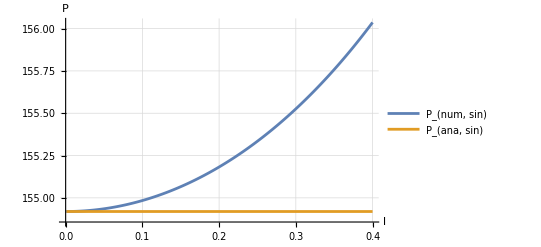

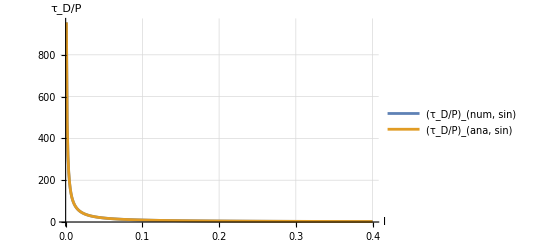

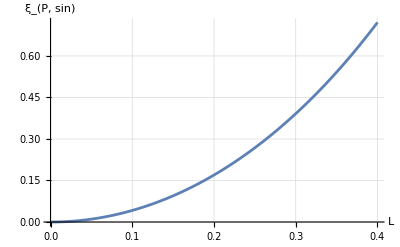

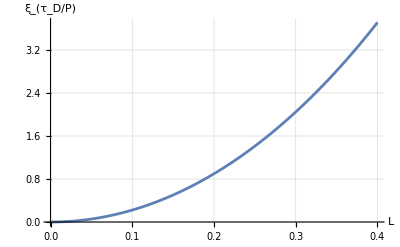

```mathematica
ListLinePlot[{PSinNumlist,PSinAnalist},AxesLabel->{"l","P"},PlotLegends->{"P_(num, sin)","P_(ana, sin)"},PlotRange->All,GridLines->Automatic]
ListLinePlot[{DampSinNumlist,DampSinAnalist},AxesLabel->{"l","τ_D/P"},PlotLegends->{"(τ_D/P)_(num, sin)","(τ_D/P)_(ana, sin)"},PlotRange->All,GridLines->Automatic]
ListLinePlot[ErrorPSinlist,AxesLabel->{"L","ξ_(P, sin)"},PlotRange->All,GridLines->Automatic]
ListLinePlot[ErrorDampSinlist,AxesLabel->{"L","ξ_(τ_D/P)"},PlotRange->All,GridLines->Automatic]
```

As for the results, they coincide with the concepts of the pdf files.

Regarding the accuracy of the approximations,  P_ana is generally an extremely satisfactory and appropriate approximation of P_num for the values of l considered with errors between solutions not surpassing the 1 %. However, (τ_D/P)_ana is a slightly worse approximation of (τ_D/P)_num for the values of l considered, with errors between solutions not surpassing the 4 %. In essence, these analytic expressions are remarkably accurate in the TTTB approximation for this density profile.

Discuss how the results would change if a linear variation of density in the nonuniform transitional layer was used instead.

```mathematica
Flin=Simplify[4/Pi^2];(*From the pdf files attached with this code*)
F=Flin;(*Linear variation of density in the nonuniform transitional layer*)
PLinNumlist={};
PLinAnalist={};
ErrorPLinlist={};
DampLinNumlist={};
DampLinAnalist={};
ErrorDampLinlist={};
initialguess=Simplify[kz*Sqrt[vk2]-I*(Pi*m*(ρi-ρe)^2*kz*Sqrt[vk2])/(8*R*(ρi+ρe)*dρr)];(*Analytical TTTB dispersion relation solution*)
(*From the pdf files attached with this code*)
Do[ωLinNum=FindRoot[DispRelation==0,{ω,initialguess}][[1,2]];
PLinNum=Simplify[(2Pi)/Re[ωLinNum]];
DampLinNum=Simplify[Re[ωLinNum]/(2 Pi Abs[Im[ωLinNum]])];
PLinAna=Simplify[(2 L)/Sqrt[vai2] Sqrt[(ρi+ρe)/(2ρi)]];(*Analytical TTTB formula for the period (does not depend on l -> constant)*)
DampLinAna=Simplify[F R/l(ρi+ρe)/(ρi-ρe)];(*Analytical TTTB formula for the damping time*)
AppendTo[PLinNumlist,{l,PLinNum}];
AppendTo[DampLinNumlist,{l,DampLinNum}];
AppendTo[PLinAnalist,{l,PLinAna}];
AppendTo[DampLinAnalist,{l,DampLinAna}];
AppendTo[ErrorPLinlist,{l,Simplify[(PLinNum-PLinAna)/PLinAna 100]}];
AppendTo[ErrorDampLinlist,{l,Simplify[(DampLinAna-DampLinNum)/DampLinAna 100]}];
initialguess=ωLinNum;,{l,llist}];
```

```mathematica
Print["{l,P_(num, lin)} (Numerical TTTB period for a linear variation of density in the nonuniform transitional layer):",PLinNumlist]
```

{l,P_(num, lin)} (Numerical TTTB period for a linear variation of density in the nonuniform transitional layer):{{0.001,154.919},{0.002,154.919},{0.003,154.919},{0.004,154.92},{0.005,154.92},{0.006,154.92},{0.007,154.92},{0.008,154.92},{0.009,154.921},{0.01,154.921},{0.011,154.921},{0.012,154.922},{0.013,154.922},{0.014,154.922},{0.015,154.923},{0.016,154.923},{0.017,154.924},{0.018,154.924},{0.019,154.925},{0.02,154.926},{0.021,154.926},{0.022,154.927},{0.023,154.928},{0.024,154.929},{0.025,154.929},{0.026,154.93},{0.027,154.931},{0.028,154.932},{0.029,154.933},{0.03,154.934},{0.031,154.935},{0.032,154.936},{0.033,154.937},{0.034,154.938},{0.035,154.939},{0.036,154.94},{0.037,154.941},{0.038,154.942},{0.039,154.944},{0.04,154.945},{0.041,154.946},{0.042,154.947},{0.043,154.949},{0.044,154.95},{0.045,154.952},{0.046,154.953},{0.047,154.955},{0.048,154.956},{0.049,154.958},{0.05,154.959},{0.051,154.961},{0.052,154.963},{0.053,154.964},{0.054,154.966},{0.055,154.968},{0.056,154.969},{0.057,154.971},{0.058,154.973},{0.059,154.975},{0.06,154.977},{0.061,154.979},{0.062,154.981},{0.063,154.983},{0.064,154.985},{0.065,154.987},{0.066,154.989},{0.067,154.991},{0.068,154.993},{0.069,154.996},{0.07,154.998},{0.071,155.},{0.072,155.002},{0.073,155.005},{0.074,155.007},{0.075,155.01},{0.076,155.012},{0.077,155.014},{0.078,155.017},{0.079,155.019},{0.08,155.022},{0.081,155.025},{0.082,155.027},{0.083,155.03},{0.084,155.033},{0.085,155.035},{0.086,155.038},{0.087,155.041},{0.088,155.044},{0.089,155.047},{0.09,155.05},{0.091,155.052},{0.092,155.055},{0.093,155.058},{0.094,155.061},{0.095,155.065},{0.096,155.068},{0.097,155.071},{0.098,155.074},{0.099,155.077},{0.1,155.08},{0.101,155.084},{0.102,155.087},{0.103,155.09},{0.104,155.094},{0.105,155.097},{0.106,155.101},{0.107,155.104},{0.108,155.108},{0.109,155.111},{0.11,155.115},{0.111,155.118},{0.112,155.122},{0.113,155.126},{0.114,155.129},{0.115,155.133},{0.116,155.137},{0.117,155.141},{0.118,155.145},{0.119,155.149},{0.12,155.153},{0.121,155.156},{0.122,155.16},{0.123,155.165},{0.124,155.169},{0.125,155.173},{0.126,155.177},{0.127,155.181},{0.128,155.185},{0.129,155.19},{0.13,155.194},{0.131,155.198},{0.132,155.202},{0.133,155.207},{0.134,155.211},{0.135,155.216},{0.136,155.22},{0.137,155.225},{0.138,155.229},{0.139,155.234},{0.14,155.239},{0.141,155.243},{0.142,155.248},{0.143,155.253},{0.144,155.258},{0.145,155.262},{0.146,155.267},{0.147,155.272},{0.148,155.277},{0.149,155.282},{0.15,155.287},{0.151,155.292},{0.152,155.297},{0.153,155.302},{0.154,155.308},{0.155,155.313},{0.156,155.318},{0.157,155.323},{0.158,155.329},{0.159,155.334},{0.16,155.339},{0.161,155.345},{0.162,155.35},{0.163,155.356},{0.164,155.361},{0.165,155.367},{0.166,155.373},{0.167,155.378},{0.168,155.384},{0.169,155.39},{0.17,155.395},{0.171,155.401},{0.172,155.407},{0.173,155.413},{0.174,155.419},{0.175,155.425},{0.176,155.431},{0.177,155.437},{0.178,155.443},{0.179,155.449},{0.18,155.455},{0.181,155.462},{0.182,155.468},{0.183,155.474},{0.184,155.48},{0.185,155.487},{0.186,155.493},{0.187,155.5},{0.188,155.506},{0.189,155.513},{0.19,155.519},{0.191,155.526},{0.192,155.532},{0.193,155.539},{0.194,155.546},{0.195,155.553},{0.196,155.56},{0.197,155.566},{0.198,155.573},{0.199,155.58},{0.2,155.587},{0.201,155.594},{0.202,155.601},{0.203,155.608},{0.204,155.616},{0.205,155.623},{0.206,155.63},{0.207,155.637},{0.208,155.645},{0.209,155.652},{0.21,155.659},{0.211,155.667},{0.212,155.674},{0.213,155.682},{0.214,155.689},{0.215,155.697},{0.216,155.705},{0.217,155.712},{0.218,155.72},{0.219,155.728},{0.22,155.736},{0.221,155.744},{0.222,155.752},{0.223,155.76},{0.224,155.768},{0.225,155.776},{0.226,155.784},{0.227,155.792},{0.228,155.8},{0.229,155.809},{0.23,155.817},{0.231,155.825},{0.232,155.834},{0.233,155.842},{0.234,155.851},{0.235,155.859},{0.236,155.868},{0.237,155.876},{0.238,155.885},{0.239,155.894},{0.24,155.902},{0.241,155.911},{0.242,155.92},{0.243,155.929},{0.244,155.938},{0.245,155.947},{0.246,155.956},{0.247,155.965},{0.248,155.974},{0.249,155.984},{0.25,155.993},{0.251,156.002},{0.252,156.011},{0.253,156.021},{0.254,156.03},{0.255,156.04},{0.256,156.049},{0.257,156.059},{0.258,156.069},{0.259,156.078},{0.26,156.088},{0.261,156.098},{0.262,156.108},{0.263,156.118},{0.264,156.128},{0.265,156.138},{0.266,156.148},{0.267,156.158},{0.268,156.168},{0.269,156.178},{0.27,156.188},{0.271,156.199},{0.272,156.209},{0.273,156.22},{0.274,156.23},{0.275,156.241},{0.276,156.251},{0.277,156.262},{0.278,156.273},{0.279,156.283},{0.28,156.294},{0.281,156.305},{0.282,156.316},{0.283,156.327},{0.284,156.338},{0.285,156.349},{0.286,156.36},{0.287,156.371},{0.288,156.383},{0.289,156.394},{0.29,156.405},{0.291,156.417},{0.292,156.428},{0.293,156.44},{0.294,156.451},{0.295,156.463},{0.296,156.475},{0.297,156.487},{0.298,156.499},{0.299,156.51},{0.3,156.522},{0.301,156.534},{0.302,156.547},{0.303,156.559},{0.304,156.571},{0.305,156.583},{0.306,156.596},{0.307,156.608},{0.308,156.62},{0.309,156.633},{0.31,156.645},{0.311,156.658},{0.312,156.671},{0.313,156.684},{0.314,156.696},{0.315,156.709},{0.316,156.722},{0.317,156.735},{0.318,156.748},{0.319,156.762},{0.32,156.775},{0.321,156.788},{0.322,156.802},{0.323,156.815},{0.324,156.828},{0.325,156.842},{0.326,156.856},{0.327,156.869},{0.328,156.883},{0.329,156.897},{0.33,156.911},{0.331,156.925},{0.332,156.939},{0.333,156.953},{0.334,156.967},{0.335,156.981},{0.336,156.996},{0.337,157.01},{0.338,157.025},{0.339,157.039},{0.34,157.054},{0.341,157.069},{0.342,157.083},{0.343,157.098},{0.344,157.113},{0.345,157.128},{0.346,157.143},{0.347,157.158},{0.348,157.174},{0.349,157.189},{0.35,157.204},{0.351,157.22},{0.352,157.235},{0.353,157.251},{0.354,157.267},{0.355,157.282},{0.356,157.298},{0.357,157.314},{0.358,157.33},{0.359,157.346},{0.36,157.362},{0.361,157.379},{0.362,157.395},{0.363,157.411},{0.364,157.428},{0.365,157.444},{0.366,157.461},{0.367,157.478},{0.368,157.495},{0.369,157.512},{0.37,157.529},{0.371,157.546},{0.372,157.563},{0.373,157.58},{0.374,157.598},{0.375,157.615},{0.376,157.633},{0.377,157.65},{0.378,157.668},{0.379,157.686},{0.38,157.704},{0.381,157.722},{0.382,157.74},{0.383,157.758},{0.384,157.776},{0.385,157.795},{0.386,157.813},{0.387,157.832},{0.388,157.85},{0.389,157.869},{0.39,157.888},{0.391,157.907},{0.392,157.926},{0.393,157.945},{0.394,157.965},{0.395,157.984},{0.396,158.003},{0.397,158.023},{0.398,158.043},{0.399,158.062},{0.4,158.082}}

```mathematica
Print["{l,P_(ana, lin)} (Analytical TTTB period for a linear variation of density in the nonuniform transitional layer):",PLinAnalist]
```

{l,P_(ana, lin)} (Analytical TTTB period for a linear variation of density in the nonuniform transitional layer):{{0.001,154.919},{0.002,154.919},{0.003,154.919},{0.004,154.919},{0.005,154.919},{0.006,154.919},{0.007,154.919},{0.008,154.919},{0.009,154.919},{0.01,154.919},{0.011,154.919},{0.012,154.919},{0.013,154.919},{0.014,154.919},{0.015,154.919},{0.016,154.919},{0.017,154.919},{0.018,154.919},{0.019,154.919},{0.02,154.919},{0.021,154.919},{0.022,154.919},{0.023,154.919},{0.024,154.919},{0.025,154.919},{0.026,154.919},{0.027,154.919},{0.028,154.919},{0.029,154.919},{0.03,154.919},{0.031,154.919},{0.032,154.919},{0.033,154.919},{0.034,154.919},{0.035,154.919},{0.036,154.919},{0.037,154.919},{0.038,154.919},{0.039,154.919},{0.04,154.919},{0.041,154.919},{0.042,154.919},{0.043,154.919},{0.044,154.919},{0.045,154.919},{0.046,154.919},{0.047,154.919},{0.048,154.919},{0.049,154.919},{0.05,154.919},{0.051,154.919},{0.052,154.919},{0.053,154.919},{0.054,154.919},{0.055,154.919},{0.056,154.919},{0.057,154.919},{0.058,154.919},{0.059,154.919},{0.06,154.919},{0.061,154.919},{0.062,154.919},{0.063,154.919},{0.064,154.919},{0.065,154.919},{0.066,154.919},{0.067,154.919},{0.068,154.919},{0.069,154.919},{0.07,154.919},{0.071,154.919},{0.072,154.919},{0.073,154.919},{0.074,154.919},{0.075,154.919},{0.076,154.919},{0.077,154.919},{0.078,154.919},{0.079,154.919},{0.08,154.919},{0.081,154.919},{0.082,154.919},{0.083,154.919},{0.084,154.919},{0.085,154.919},{0.086,154.919},{0.087,154.919},{0.088,154.919},{0.089,154.919},{0.09,154.919},{0.091,154.919},{0.092,154.919},{0.093,154.919},{0.094,154.919},{0.095,154.919},{0.096,154.919},{0.097,154.919},{0.098,154.919},{0.099,154.919},{0.1,154.919},{0.101,154.919},{0.102,154.919},{0.103,154.919},{0.104,154.919},{0.105,154.919},{0.106,154.919},{0.107,154.919},{0.108,154.919},{0.109,154.919},{0.11,154.919},{0.111,154.919},{0.112,154.919},{0.113,154.919},{0.114,154.919},{0.115,154.919},{0.116,154.919},{0.117,154.919},{0.118,154.919},{0.119,154.919},{0.12,154.919},{0.121,154.919},{0.122,154.919},{0.123,154.919},{0.124,154.919},{0.125,154.919},{0.126,154.919},{0.127,154.919},{0.128,154.919},{0.129,154.919},{0.13,154.919},{0.131,154.919},{0.132,154.919},{0.133,154.919},{0.134,154.919},{0.135,154.919},{0.136,154.919},{0.137,154.919},{0.138,154.919},{0.139,154.919},{0.14,154.919},{0.141,154.919},{0.142,154.919},{0.143,154.919},{0.144,154.919},{0.145,154.919},{0.146,154.919},{0.147,154.919},{0.148,154.919},{0.149,154.919},{0.15,154.919},{0.151,154.919},{0.152,154.919},{0.153,154.919},{0.154,154.919},{0.155,154.919},{0.156,154.919},{0.157,154.919},{0.158,154.919},{0.159,154.919},{0.16,154.919},{0.161,154.919},{0.162,154.919},{0.163,154.919},{0.164,154.919},{0.165,154.919},{0.166,154.919},{0.167,154.919},{0.168,154.919},{0.169,154.919},{0.17,154.919},{0.171,154.919},{0.172,154.919},{0.173,154.919},{0.174,154.919},{0.175,154.919},{0.176,154.919},{0.177,154.919},{0.178,154.919},{0.179,154.919},{0.18,154.919},{0.181,154.919},{0.182,154.919},{0.183,154.919},{0.184,154.919},{0.185,154.919},{0.186,154.919},{0.187,154.919},{0.188,154.919},{0.189,154.919},{0.19,154.919},{0.191,154.919},{0.192,154.919},{0.193,154.919},{0.194,154.919},{0.195,154.919},{0.196,154.919},{0.197,154.919},{0.198,154.919},{0.199,154.919},{0.2,154.919},{0.201,154.919},{0.202,154.919},{0.203,154.919},{0.204,154.919},{0.205,154.919},{0.206,154.919},{0.207,154.919},{0.208,154.919},{0.209,154.919},{0.21,154.919},{0.211,154.919},{0.212,154.919},{0.213,154.919},{0.214,154.919},{0.215,154.919},{0.216,154.919},{0.217,154.919},{0.218,154.919},{0.219,154.919},{0.22,154.919},{0.221,154.919},{0.222,154.919},{0.223,154.919},{0.224,154.919},{0.225,154.919},{0.226,154.919},{0.227,154.919},{0.228,154.919},{0.229,154.919},{0.23,154.919},{0.231,154.919},{0.232,154.919},{0.233,154.919},{0.234,154.919},{0.235,154.919},{0.236,154.919},{0.237,154.919},{0.238,154.919},{0.239,154.919},{0.24,154.919},{0.241,154.919},{0.242,154.919},{0.243,154.919},{0.244,154.919},{0.245,154.919},{0.246,154.919},{0.247,154.919},{0.248,154.919},{0.249,154.919},{0.25,154.919},{0.251,154.919},{0.252,154.919},{0.253,154.919},{0.254,154.919},{0.255,154.919},{0.256,154.919},{0.257,154.919},{0.258,154.919},{0.259,154.919},{0.26,154.919},{0.261,154.919},{0.262,154.919},{0.263,154.919},{0.264,154.919},{0.265,154.919},{0.266,154.919},{0.267,154.919},{0.268,154.919},{0.269,154.919},{0.27,154.919},{0.271,154.919},{0.272,154.919},{0.273,154.919},{0.274,154.919},{0.275,154.919},{0.276,154.919},{0.277,154.919},{0.278,154.919},{0.279,154.919},{0.28,154.919},{0.281,154.919},{0.282,154.919},{0.283,154.919},{0.284,154.919},{0.285,154.919},{0.286,154.919},{0.287,154.919},{0.288,154.919},{0.289,154.919},{0.29,154.919},{0.291,154.919},{0.292,154.919},{0.293,154.919},{0.294,154.919},{0.295,154.919},{0.296,154.919},{0.297,154.919},{0.298,154.919},{0.299,154.919},{0.3,154.919},{0.301,154.919},{0.302,154.919},{0.303,154.919},{0.304,154.919},{0.305,154.919},{0.306,154.919},{0.307,154.919},{0.308,154.919},{0.309,154.919},{0.31,154.919},{0.311,154.919},{0.312,154.919},{0.313,154.919},{0.314,154.919},{0.315,154.919},{0.316,154.919},{0.317,154.919},{0.318,154.919},{0.319,154.919},{0.32,154.919},{0.321,154.919},{0.322,154.919},{0.323,154.919},{0.324,154.919},{0.325,154.919},{0.326,154.919},{0.327,154.919},{0.328,154.919},{0.329,154.919},{0.33,154.919},{0.331,154.919},{0.332,154.919},{0.333,154.919},{0.334,154.919},{0.335,154.919},{0.336,154.919},{0.337,154.919},{0.338,154.919},{0.339,154.919},{0.34,154.919},{0.341,154.919},{0.342,154.919},{0.343,154.919},{0.344,154.919},{0.345,154.919},{0.346,154.919},{0.347,154.919},{0.348,154.919},{0.349,154.919},{0.35,154.919},{0.351,154.919},{0.352,154.919},{0.353,154.919},{0.354,154.919},{0.355,154.919},{0.356,154.919},{0.357,154.919},{0.358,154.919},{0.359,154.919},{0.36,154.919},{0.361,154.919},{0.362,154.919},{0.363,154.919},{0.364,154.919},{0.365,154.919},{0.366,154.919},{0.367,154.919},{0.368,154.919},{0.369,154.919},{0.37,154.919},{0.371,154.919},{0.372,154.919},{0.373,154.919},{0.374,154.919},{0.375,154.919},{0.376,154.919},{0.377,154.919},{0.378,154.919},{0.379,154.919},{0.38,154.919},{0.381,154.919},{0.382,154.919},{0.383,154.919},{0.384,154.919},{0.385,154.919},{0.386,154.919},{0.387,154.919},{0.388,154.919},{0.389,154.919},{0.39,154.919},{0.391,154.919},{0.392,154.919},{0.393,154.919},{0.394,154.919},{0.395,154.919},{0.396,154.919},{0.397,154.919},{0.398,154.919},{0.399,154.919},{0.4,154.919}}

```mathematica
Print["{l,(τ_D/P)_(num, lin)} (Numerical TTTB damping time for a linear variation of density in the nonuniform transitional layer):",DampLinNumlist]
```

{l,(τ_D/P)_(num, lin)} (Numerical TTTB damping time for a linear variation of density in the nonuniform transitional layer):{{0.001,607.927},{0.002,303.963},{0.003,202.641},{0.004,151.98},{0.005,121.584},{0.006,101.319},{0.007,86.8444},{0.008,75.9882},{0.009,67.5445},{0.01,60.7894},{0.011,55.2624},{0.012,50.6566},{0.013,46.7593},{0.014,43.4187},{0.015,40.5235},{0.016,37.9901},{0.017,35.7548},{0.018,33.7677},{0.019,31.9898},{0.02,30.3897},{0.021,28.9419},{0.022,27.6257},{0.023,26.4239},{0.024,25.3223},{0.025,24.3087},{0.026,23.3731},{0.027,22.5068},{0.028,21.7023},{0.029,20.9533},{0.03,20.2542},{0.031,19.6002},{0.032,18.987},{0.033,18.411},{0.034,17.8689},{0.035,17.3577},{0.036,16.8749},{0.037,16.4181},{0.038,15.9854},{0.039,15.5749},{0.04,15.1848},{0.041,14.8138},{0.042,14.4604},{0.043,14.1235},{0.044,13.8018},{0.045,13.4945},{0.046,13.2005},{0.047,12.9189},{0.048,12.6491},{0.049,12.3903},{0.05,12.1418},{0.051,11.9031},{0.052,11.6735},{0.053,11.4526},{0.054,11.2399},{0.055,11.0349},{0.056,10.8371},{0.057,10.6463},{0.058,10.4621},{0.059,10.2841},{0.06,10.1121},{0.061,9.94564},{0.062,9.78456},{0.063,9.62858},{0.064,9.47747},{0.065,9.331},{0.066,9.18896},{0.067,9.05114},{0.068,8.91737},{0.069,8.78747},{0.07,8.66127},{0.071,8.53861},{0.072,8.41935},{0.073,8.30335},{0.074,8.19048},{0.075,8.08061},{0.076,7.97362},{0.077,7.86939},{0.078,7.76784},{0.079,7.66884},{0.08,7.57231},{0.081,7.47816},{0.082,7.3863},{0.083,7.29664},{0.084,7.2091},{0.085,7.12362},{0.086,7.04012},{0.087,6.95853},{0.088,6.87879},{0.089,6.80083},{0.09,6.72459},{0.091,6.65003},{0.092,6.57707},{0.093,6.50568},{0.094,6.4358},{0.095,6.36739},{0.096,6.30039},{0.097,6.23476},{0.098,6.17047},{0.099,6.10747},{0.1,6.04573},{0.101,5.9852},{0.102,5.92585},{0.103,5.86764},{0.104,5.81055},{0.105,5.75454},{0.106,5.69958},{0.107,5.64564},{0.108,5.59269},{0.109,5.54071},{0.11,5.48966},{0.111,5.43953},{0.112,5.39029},{0.113,5.34191},{0.114,5.29438},{0.115,5.24767},{0.116,5.20175},{0.117,5.15662},{0.118,5.11224},{0.119,5.06861},{0.12,5.02569},{0.121,4.98348},{0.122,4.94196},{0.123,4.9011},{0.124,4.8609},{0.125,4.82133},{0.126,4.78239},{0.127,4.74406},{0.128,4.70632},{0.129,4.66916},{0.13,4.63256},{0.131,4.59652},{0.132,4.56102},{0.133,4.52605},{0.134,4.49159},{0.135,4.45764},{0.136,4.42418},{0.137,4.39121},{0.138,4.35871},{0.139,4.32667},{0.14,4.29508},{0.141,4.26394},{0.142,4.23323},{0.143,4.20295},{0.144,4.17308},{0.145,4.14361},{0.146,4.11455},{0.147,4.08588},{0.148,4.05759},{0.149,4.02967},{0.15,4.00212},{0.151,3.97494},{0.152,3.9481},{0.153,3.92161},{0.154,3.89546},{0.155,3.86964},{0.156,3.84415},{0.157,3.81898},{0.158,3.79412},{0.159,3.76958},{0.16,3.74533},{0.161,3.72138},{0.162,3.69772},{0.163,3.67435},{0.164,3.65125},{0.165,3.62844},{0.166,3.60589},{0.167,3.58361},{0.168,3.56159},{0.169,3.53982},{0.17,3.51831},{0.171,3.49705},{0.172,3.47602},{0.173,3.45524},{0.174,3.43469},{0.175,3.41437},{0.176,3.39428},{0.177,3.37441},{0.178,3.35476},{0.179,3.33533},{0.18,3.31611},{0.181,3.29709},{0.182,3.27828},{0.183,3.25967},{0.184,3.24126},{0.185,3.22305},{0.186,3.20502},{0.187,3.18719},{0.188,3.16954},{0.189,3.15207},{0.19,3.13479},{0.191,3.11768},{0.192,3.10074},{0.193,3.08398},{0.194,3.06738},{0.195,3.05095},{0.196,3.03469},{0.197,3.01858},{0.198,3.00264},{0.199,2.98685},{0.2,2.97121},{0.201,2.95573},{0.202,2.9404},{0.203,2.92521},{0.204,2.91017},{0.205,2.89527},{0.206,2.88051},{0.207,2.86589},{0.208,2.85141},{0.209,2.83706},{0.21,2.82285},{0.211,2.80876},{0.212,2.79481},{0.213,2.78098},{0.214,2.76728},{0.215,2.7537},{0.216,2.74025},{0.217,2.72691},{0.218,2.71369},{0.219,2.70059},{0.22,2.68761},{0.221,2.67474},{0.222,2.66198},{0.223,2.64933},{0.224,2.63679},{0.225,2.62436},{0.226,2.61204},{0.227,2.59982},{0.228,2.5877},{0.229,2.57569},{0.23,2.56378},{0.231,2.55196},{0.232,2.54025},{0.233,2.52863},{0.234,2.51711},{0.235,2.50568},{0.236,2.49435},{0.237,2.48311},{0.238,2.47196},{0.239,2.46089},{0.24,2.44992},{0.241,2.43904},{0.242,2.42824},{0.243,2.41752},{0.244,2.4069},{0.245,2.39635},{0.246,2.38589},{0.247,2.37551},{0.248,2.3652},{0.249,2.35498},{0.25,2.34484},{0.251,2.33477},{0.252,2.32478},{0.253,2.31487},{0.254,2.30503},{0.255,2.29526},{0.256,2.28557},{0.257,2.27595},{0.258,2.2664},{0.259,2.25692},{0.26,2.24751},{0.261,2.23817},{0.262,2.22889},{0.263,2.21969},{0.264,2.21055},{0.265,2.20147},{0.266,2.19246},{0.267,2.18352},{0.268,2.17464},{0.269,2.16582},{0.27,2.15706},{0.271,2.14836},{0.272,2.13973},{0.273,2.13115},{0.274,2.12264},{0.275,2.11418},{0.276,2.10578},{0.277,2.09744},{0.278,2.08915},{0.279,2.08092},{0.28,2.07275},{0.281,2.06463},{0.282,2.05657},{0.283,2.04856},{0.284,2.0406},{0.285,2.03269},{0.286,2.02484},{0.287,2.01704},{0.288,2.00929},{0.289,2.00159},{0.29,1.99394},{0.291,1.98634},{0.292,1.97878},{0.293,1.97128},{0.294,1.96382},{0.295,1.95642},{0.296,1.94905},{0.297,1.94174},{0.298,1.93447},{0.299,1.92724},{0.3,1.92006},{0.301,1.91293},{0.302,1.90584},{0.303,1.89879},{0.304,1.89178},{0.305,1.88482},{0.306,1.8779},{0.307,1.87102},{0.308,1.86419},{0.309,1.85739},{0.31,1.85064},{0.311,1.84392},{0.312,1.83725},{0.313,1.83061},{0.314,1.82402},{0.315,1.81746},{0.316,1.81094},{0.317,1.80446},{0.318,1.79802},{0.319,1.79161},{0.32,1.78524},{0.321,1.77891},{0.322,1.77261},{0.323,1.76635},{0.324,1.76012},{0.325,1.75393},{0.326,1.74777},{0.327,1.74165},{0.328,1.73556},{0.329,1.72951},{0.33,1.72349},{0.331,1.7175},{0.332,1.71155},{0.333,1.70562},{0.334,1.69973},{0.335,1.69388},{0.336,1.68805},{0.337,1.68226},{0.338,1.67649},{0.339,1.67076},{0.34,1.66506},{0.341,1.65938},{0.342,1.65374},{0.343,1.64813},{0.344,1.64254},{0.345,1.63699},{0.346,1.63146},{0.347,1.62597},{0.348,1.6205},{0.349,1.61506},{0.35,1.60964},{0.351,1.60426},{0.352,1.5989},{0.353,1.59357},{0.354,1.58827},{0.355,1.58299},{0.356,1.57774},{0.357,1.57251},{0.358,1.56731},{0.359,1.56214},{0.36,1.55699},{0.361,1.55187},{0.362,1.54677},{0.363,1.5417},{0.364,1.53665},{0.365,1.53162},{0.366,1.52662},{0.367,1.52165},{0.368,1.51669},{0.369,1.51177},{0.37,1.50686},{0.371,1.50198},{0.372,1.49712},{0.373,1.49228},{0.374,1.48747},{0.375,1.48267},{0.376,1.4779},{0.377,1.47315},{0.378,1.46843},{0.379,1.46372},{0.38,1.45904},{0.381,1.45438},{0.382,1.44973},{0.383,1.44511},{0.384,1.44051},{0.385,1.43593},{0.386,1.43138},{0.387,1.42684},{0.388,1.42232},{0.389,1.41782},{0.39,1.41334},{0.391,1.40888},{0.392,1.40444},{0.393,1.40001},{0.394,1.39561},{0.395,1.39123},{0.396,1.38686},{0.397,1.38251},{0.398,1.37818},{0.399,1.37387},{0.4,1.36958}}

```mathematica
Print["{l,(τ_D/P)_(ana, lin)} (Analytical TTTB damping time for a linear variation of density in the nonuniform transitional layer):",DampLinAnalist]
```

{l,(τ_D/P)_(ana, lin)} (Analytical TTTB damping time for a linear variation of density in the nonuniform transitional layer):{{0.001,607.927},{0.002,303.964},{0.003,202.642},{0.004,151.982},{0.005,121.585},{0.006,101.321},{0.007,86.8467},{0.008,75.9909},{0.009,67.5475},{0.01,60.7927},{0.011,55.2661},{0.012,50.6606},{0.013,46.7636},{0.014,43.4234},{0.015,40.5285},{0.016,37.9954},{0.017,35.7604},{0.018,33.7737},{0.019,31.9962},{0.02,30.3964},{0.021,28.9489},{0.022,27.6331},{0.023,26.4316},{0.024,25.3303},{0.025,24.3171},{0.026,23.3818},{0.027,22.5158},{0.028,21.7117},{0.029,20.963},{0.03,20.2642},{0.031,19.6106},{0.032,18.9977},{0.033,18.422},{0.034,17.8802},{0.035,17.3693},{0.036,16.8869},{0.037,16.4305},{0.038,15.9981},{0.039,15.5879},{0.04,15.1982},{0.041,14.8275},{0.042,14.4745},{0.043,14.1378},{0.044,13.8165},{0.045,13.5095},{0.046,13.2158},{0.047,12.9346},{0.048,12.6651},{0.049,12.4067},{0.05,12.1585},{0.051,11.9201},{0.052,11.6909},{0.053,11.4703},{0.054,11.2579},{0.055,11.0532},{0.056,10.8558},{0.057,10.6654},{0.058,10.4815},{0.059,10.3038},{0.06,10.1321},{0.061,9.96602},{0.062,9.80528},{0.063,9.64964},{0.064,9.49886},{0.065,9.35272},{0.066,9.21102},{0.067,9.07354},{0.068,8.9401},{0.069,8.81054},{0.07,8.68467},{0.071,8.56235},{0.072,8.44343},{0.073,8.32777},{0.074,8.21523},{0.075,8.10569},{0.076,7.99904},{0.077,7.89516},{0.078,7.79394},{0.079,7.69528},{0.08,7.59909},{0.081,7.50527},{0.082,7.41375},{0.083,7.32442},{0.084,7.23723},{0.085,7.15208},{0.086,7.06892},{0.087,6.98767},{0.088,6.90826},{0.089,6.83064},{0.09,6.75475},{0.091,6.68052},{0.092,6.6079},{0.093,6.53685},{0.094,6.46731},{0.095,6.39923},{0.096,6.33257},{0.097,6.26729},{0.098,6.20334},{0.099,6.14068},{0.1,6.07927},{0.101,6.01908},{0.102,5.96007},{0.103,5.9022},{0.104,5.84545},{0.105,5.78978},{0.106,5.73516},{0.107,5.68156},{0.108,5.62895},{0.109,5.57731},{0.11,5.52661},{0.111,5.47682},{0.112,5.42792},{0.113,5.37989},{0.114,5.33269},{0.115,5.28632},{0.116,5.24075},{0.117,5.19596},{0.118,5.15192},{0.119,5.10863},{0.12,5.06606},{0.121,5.02419},{0.122,4.98301},{0.123,4.9425},{0.124,4.90264},{0.125,4.86342},{0.126,4.82482},{0.127,4.78683},{0.128,4.74943},{0.129,4.71261},{0.13,4.67636},{0.131,4.64066},{0.132,4.60551},{0.133,4.57088},{0.134,4.53677},{0.135,4.50316},{0.136,4.47005},{0.137,4.43742},{0.138,4.40527},{0.139,4.37358},{0.14,4.34234},{0.141,4.31154},{0.142,4.28118},{0.143,4.25124},{0.144,4.22172},{0.145,4.1926},{0.146,4.16388},{0.147,4.13556},{0.148,4.10762},{0.149,4.08005},{0.15,4.05285},{0.151,4.02601},{0.152,3.99952},{0.153,3.97338},{0.154,3.94758},{0.155,3.92211},{0.156,3.89697},{0.157,3.87215},{0.158,3.84764},{0.159,3.82344},{0.16,3.79954},{0.161,3.77594},{0.162,3.75264},{0.163,3.72961},{0.164,3.70687},{0.165,3.68441},{0.166,3.66221},{0.167,3.64028},{0.168,3.61861},{0.169,3.5972},{0.17,3.57604},{0.171,3.55513},{0.172,3.53446},{0.173,3.51403},{0.174,3.49383},{0.175,3.47387},{0.176,3.45413},{0.177,3.43462},{0.178,3.41532},{0.179,3.39624},{0.18,3.37737},{0.181,3.35871},{0.182,3.34026},{0.183,3.32201},{0.184,3.30395},{0.185,3.28609},{0.186,3.26843},{0.187,3.25095},{0.188,3.23365},{0.189,3.21655},{0.19,3.19962},{0.191,3.18286},{0.192,3.16629},{0.193,3.14988},{0.194,3.13364},{0.195,3.11757},{0.196,3.10167},{0.197,3.08592},{0.198,3.07034},{0.199,3.05491},{0.2,3.03964},{0.201,3.02451},{0.202,3.00954},{0.203,2.99471},{0.204,2.98003},{0.205,2.9655},{0.206,2.9511},{0.207,2.93685},{0.208,2.92273},{0.209,2.90874},{0.21,2.89489},{0.211,2.88117},{0.212,2.86758},{0.213,2.85412},{0.214,2.84078},{0.215,2.82757},{0.216,2.81448},{0.217,2.80151},{0.218,2.78866},{0.219,2.77592},{0.22,2.76331},{0.221,2.7508},{0.222,2.73841},{0.223,2.72613},{0.224,2.71396},{0.225,2.7019},{0.226,2.68994},{0.227,2.67809},{0.228,2.66635},{0.229,2.6547},{0.23,2.64316},{0.231,2.63172},{0.232,2.62038},{0.233,2.60913},{0.234,2.59798},{0.235,2.58692},{0.236,2.57596},{0.237,2.56509},{0.238,2.55432},{0.239,2.54363},{0.24,2.53303},{0.241,2.52252},{0.242,2.5121},{0.243,2.50176},{0.244,2.4915},{0.245,2.48134},{0.246,2.47125},{0.247,2.46124},{0.248,2.45132},{0.249,2.44147},{0.25,2.43171},{0.251,2.42202},{0.252,2.41241},{0.253,2.40287},{0.254,2.39341},{0.255,2.38403},{0.256,2.37472},{0.257,2.36548},{0.258,2.35631},{0.259,2.34721},{0.26,2.33818},{0.261,2.32922},{0.262,2.32033},{0.263,2.31151},{0.264,2.30275},{0.265,2.29406},{0.266,2.28544},{0.267,2.27688},{0.268,2.26838},{0.269,2.25995},{0.27,2.25158},{0.271,2.24327},{0.272,2.23503},{0.273,2.22684},{0.274,2.21871},{0.275,2.21064},{0.276,2.20263},{0.277,2.19468},{0.278,2.18679},{0.279,2.17895},{0.28,2.17117},{0.281,2.16344},{0.282,2.15577},{0.283,2.14815},{0.284,2.14059},{0.285,2.13308},{0.286,2.12562},{0.287,2.11821},{0.288,2.11086},{0.289,2.10355},{0.29,2.0963},{0.291,2.0891},{0.292,2.08194},{0.293,2.07484},{0.294,2.06778},{0.295,2.06077},{0.296,2.05381},{0.297,2.04689},{0.298,2.04002},{0.299,2.0332},{0.3,2.02642},{0.301,2.01969},{0.302,2.013},{0.303,2.00636},{0.304,1.99976},{0.305,1.9932},{0.306,1.98669},{0.307,1.98022},{0.308,1.97379},{0.309,1.9674},{0.31,1.96106},{0.311,1.95475},{0.312,1.94848},{0.313,1.94226},{0.314,1.93607},{0.315,1.92993},{0.316,1.92382},{0.317,1.91775},{0.318,1.91172},{0.319,1.90573},{0.32,1.89977},{0.321,1.89385},{0.322,1.88797},{0.323,1.88213},{0.324,1.87632},{0.325,1.87054},{0.326,1.86481},{0.327,1.8591},{0.328,1.85344},{0.329,1.8478},{0.33,1.8422},{0.331,1.83664},{0.332,1.83111},{0.333,1.82561},{0.334,1.82014},{0.335,1.81471},{0.336,1.80931},{0.337,1.80394},{0.338,1.7986},{0.339,1.7933},{0.34,1.78802},{0.341,1.78278},{0.342,1.77756},{0.343,1.77238},{0.344,1.76723},{0.345,1.76211},{0.346,1.75701},{0.347,1.75195},{0.348,1.74692},{0.349,1.74191},{0.35,1.73693},{0.351,1.73199},{0.352,1.72707},{0.353,1.72217},{0.354,1.71731},{0.355,1.71247},{0.356,1.70766},{0.357,1.70288},{0.358,1.69812},{0.359,1.69339},{0.36,1.68869},{0.361,1.68401},{0.362,1.67936},{0.363,1.67473},{0.364,1.67013},{0.365,1.66555},{0.366,1.661},{0.367,1.65648},{0.368,1.65198},{0.369,1.6475},{0.37,1.64305},{0.371,1.63862},{0.372,1.63421},{0.373,1.62983},{0.374,1.62547},{0.375,1.62114},{0.376,1.61683},{0.377,1.61254},{0.378,1.60827},{0.379,1.60403},{0.38,1.59981},{0.381,1.59561},{0.382,1.59143},{0.383,1.58728},{0.384,1.58314},{0.385,1.57903},{0.386,1.57494},{0.387,1.57087},{0.388,1.56682},{0.389,1.56279},{0.39,1.55879},{0.391,1.5548},{0.392,1.55083},{0.393,1.54689},{0.394,1.54296},{0.395,1.53906},{0.396,1.53517},{0.397,1.5313},{0.398,1.52746},{0.399,1.52363},{0.4,1.51982}}

```mathematica
Print["{l,ξ_(P, lin)} (Error percentage between numerical and analytical periods for a linear variation of density in the nonuniform transitional layer):",ErrorPLinlist]
```

{l,ξ_(P, lin)} (Error percentage between numerical and analytical periods for a linear variation of density in the nonuniform transitional layer):{{0.001,0.0000102808},{0.002,0.0000411235},{0.003,0.0000925285},{0.004,0.000164496},{0.005,0.000257028},{0.006,0.000370125},{0.007,0.000503789},{0.008,0.000658021},{0.009,0.000832825},{0.01,0.0010282},{0.011,0.00124415},{0.012,0.00148068},{0.013,0.0017378},{0.014,0.00201549},{0.015,0.00231378},{0.016,0.00263266},{0.017,0.00297214},{0.018,0.00333222},{0.019,0.00371291},{0.02,0.00411421},{0.021,0.00453612},{0.022,0.00497866},{0.023,0.00544184},{0.024,0.00592564},{0.025,0.00643009},{0.026,0.00695519},{0.027,0.00750095},{0.028,0.00806737},{0.029,0.00865446},{0.03,0.00926223},{0.031,0.00989069},{0.032,0.0105398},{0.033,0.0112097},{0.034,0.0119003},{0.035,0.0126116},{0.036,0.0133436},{0.037,0.0140964},{0.038,0.0148699},{0.039,0.0156642},{0.04,0.0164793},{0.041,0.0173152},{0.042,0.0181719},{0.043,0.0190493},{0.044,0.0199476},{0.045,0.0208668},{0.046,0.0218067},{0.047,0.0227676},{0.048,0.0237493},{0.049,0.0247519},{0.05,0.0257754},{0.051,0.0268198},{0.052,0.0278852},{0.053,0.0289715},{0.054,0.0300787},{0.055,0.0312069},{0.056,0.0323562},{0.057,0.0335264},{0.058,0.0347176},{0.059,0.0359299},{0.06,0.0371633},{0.061,0.0384177},{0.062,0.0396932},{0.063,0.0409898},{0.064,0.0423076},{0.065,0.0436464},{0.066,0.0450065},{0.067,0.0463877},{0.068,0.0477902},{0.069,0.0492138},{0.07,0.0506587},{0.071,0.0521249},{0.072,0.0536123},{0.073,0.0551211},{0.074,0.0566511},{0.075,0.0582025},{0.076,0.0597753},{0.077,0.0613695},{0.078,0.0629851},{0.079,0.0646221},{0.08,0.0662806},{0.081,0.0679605},{0.082,0.069662},{0.083,0.071385},{0.084,0.0731295},{0.085,0.0748956},{0.086,0.0766833},{0.087,0.0784927},{0.088,0.0803237},{0.089,0.0821764},{0.09,0.0840507},{0.091,0.0859469},{0.092,0.0878647},{0.093,0.0898044},{0.094,0.0917659},{0.095,0.0937492},{0.096,0.0957544},{0.097,0.0977815},{0.098,0.0998305},{0.099,0.101901},{0.1,0.103994},{0.101,0.106109},{0.102,0.108246},{0.103,0.110406},{0.104,0.112587},{0.105,0.11479},{0.106,0.117016},{0.107,0.119263},{0.108,0.121533},{0.109,0.123826},{0.11,0.12614},{0.111,0.128477},{0.112,0.130836},{0.113,0.133218},{0.114,0.135622},{0.115,0.138049},{0.116,0.140498},{0.117,0.142969},{0.118,0.145464},{0.119,0.14798},{0.12,0.15052},{0.121,0.153082},{0.122,0.155667},{0.123,0.158275},{0.124,0.160905},{0.125,0.163559},{0.126,0.166235},{0.127,0.168934},{0.128,0.171656},{0.129,0.174401},{0.13,0.177169},{0.131,0.179961},{0.132,0.182775},{0.133,0.185612},{0.134,0.188473},{0.135,0.191357},{0.136,0.194265},{0.137,0.197195},{0.138,0.200149},{0.139,0.203127},{0.14,0.206128},{0.141,0.209152},{0.142,0.2122},{0.143,0.215272},{0.144,0.218367},{0.145,0.221486},{0.146,0.224629},{0.147,0.227796},{0.148,0.230986},{0.149,0.2342},{0.15,0.237439},{0.151,0.240701},{0.152,0.243987},{0.153,0.247298},{0.154,0.250632},{0.155,0.253991},{0.156,0.257374},{0.157,0.260782},{0.158,0.264213},{0.159,0.267669},{0.16,0.27115},{0.161,0.274655},{0.162,0.278185},{0.163,0.281739},{0.164,0.285318},{0.165,0.288922},{0.166,0.29255},{0.167,0.296204},{0.168,0.299882},{0.169,0.303585},{0.17,0.307314},{0.171,0.311067},{0.172,0.314845},{0.173,0.318649},{0.174,0.322478},{0.175,0.326333},{0.176,0.330212},{0.177,0.334117},{0.178,0.338048},{0.179,0.342004},{0.18,0.345986},{0.181,0.349994},{0.182,0.354027},{0.183,0.358087},{0.184,0.362172},{0.185,0.366283},{0.186,0.37042},{0.187,0.374584},{0.188,0.378773},{0.189,0.382989},{0.19,0.387231},{0.191,0.391499},{0.192,0.395794},{0.193,0.400115},{0.194,0.404463},{0.195,0.408838},{0.196,0.413239},{0.197,0.417668},{0.198,0.422123},{0.199,0.426605},{0.2,0.431114},{0.201,0.43565},{0.202,0.440213},{0.203,0.444804},{0.204,0.449422},{0.205,0.454068},{0.206,0.458741},{0.207,0.463441},{0.208,0.468169},{0.209,0.472925},{0.21,0.477709},{0.211,0.482521},{0.212,0.48736},{0.213,0.492228},{0.214,0.497124},{0.215,0.502048},{0.216,0.507001},{0.217,0.511982},{0.218,0.516991},{0.219,0.522029},{0.22,0.527096},{0.221,0.532191},{0.222,0.537316},{0.223,0.542469},{0.224,0.547652},{0.225,0.552863},{0.226,0.558104},{0.227,0.563374},{0.228,0.568673},{0.229,0.574002},{0.23,0.579361},{0.231,0.584749},{0.232,0.590168},{0.233,0.595616},{0.234,0.601094},{0.235,0.606602},{0.236,0.61214},{0.237,0.617709},{0.238,0.623308},{0.239,0.628938},{0.24,0.634598},{0.241,0.640289},{0.242,0.646011},{0.243,0.651763},{0.244,0.657547},{0.245,0.663362},{0.246,0.669208},{0.247,0.675086},{0.248,0.680995},{0.249,0.686936},{0.25,0.692908},{0.251,0.698912},{0.252,0.704949},{0.253,0.711017},{0.254,0.717117},{0.255,0.72325},{0.256,0.729415},{0.257,0.735613},{0.258,0.741843},{0.259,0.748106},{0.26,0.754402},{0.261,0.760731},{0.262,0.767094},{0.263,0.773489},{0.264,0.779918},{0.265,0.786381},{0.266,0.792877},{0.267,0.799407},{0.268,0.80597},{0.269,0.812568},{0.27,0.8192},{0.271,0.825867},{0.272,0.832568},{0.273,0.839303},{0.274,0.846073},{0.275,0.852879},{0.276,0.859719},{0.277,0.866594},{0.278,0.873505},{0.279,0.880451},{0.28,0.887432},{0.281,0.89445},{0.282,0.901503},{0.283,0.908593},{0.284,0.915718},{0.285,0.92288},{0.286,0.930078},{0.287,0.937313},{0.288,0.944585},{0.289,0.951894},{0.29,0.95924},{0.291,0.966623},{0.292,0.974044},{0.293,0.981503},{0.294,0.988999},{0.295,0.996533},{0.296,1.0041},{0.297,1.01172},{0.298,1.01936},{0.299,1.02705},{0.3,1.03478},{0.301,1.04254},{0.302,1.05035},{0.303,1.05819},{0.304,1.06607},{0.305,1.074},{0.306,1.08196},{0.307,1.08996},{0.308,1.09801},{0.309,1.10609},{0.31,1.11421},{0.311,1.12238},{0.312,1.13059},{0.313,1.13883},{0.314,1.14712},{0.315,1.15545},{0.316,1.16382},{0.317,1.17224},{0.318,1.18069},{0.319,1.18919},{0.32,1.19773},{0.321,1.20632},{0.322,1.21494},{0.323,1.22361},{0.324,1.23233},{0.325,1.24109},{0.326,1.24989},{0.327,1.25873},{0.328,1.26762},{0.329,1.27656},{0.33,1.28554},{0.331,1.29456},{0.332,1.30363},{0.333,1.31274},{0.334,1.3219},{0.335,1.33111},{0.336,1.34036},{0.337,1.34966},{0.338,1.35901},{0.339,1.3684},{0.34,1.37784},{0.341,1.38733},{0.342,1.39686},{0.343,1.40645},{0.344,1.41608},{0.345,1.42576},{0.346,1.43549},{0.347,1.44526},{0.348,1.45509},{0.349,1.46497},{0.35,1.47489},{0.351,1.48487},{0.352,1.4949},{0.353,1.50497},{0.354,1.5151},{0.355,1.52528},{0.356,1.53551},{0.357,1.5458},{0.358,1.55613},{0.359,1.56652},{0.36,1.57696},{0.361,1.58745},{0.362,1.598},{0.363,1.6086},{0.364,1.61925},{0.365,1.62996},{0.366,1.64073},{0.367,1.65154},{0.368,1.66242},{0.369,1.67335},{0.37,1.68433},{0.371,1.69537},{0.372,1.70647},{0.373,1.71763},{0.374,1.72884},{0.375,1.74011},{0.376,1.75144},{0.377,1.76282},{0.378,1.77427},{0.379,1.78577},{0.38,1.79734},{0.381,1.80896},{0.382,1.82065},{0.383,1.83239},{0.384,1.8442},{0.385,1.85607},{0.386,1.868},{0.387,1.87999},{0.388,1.89204},{0.389,1.90416},{0.39,1.91634},{0.391,1.92859},{0.392,1.9409},{0.393,1.95327},{0.394,1.96571},{0.395,1.97822},{0.396,1.99079},{0.397,2.00342},{0.398,2.01613},{0.399,2.0289},{0.4,2.04174}}

```mathematica
Print["{l,ξ_(τ_D/P)} (Error percentage between numerical and analytical damping times for a linear variation of density in the nonuniform transitional layer):",ErrorDampLinlist]
```

{l,ξ_(τ_D/P)} (Error percentage between numerical and analytical damping times for a linear variation of density in the nonuniform transitional layer):{{0.001,0.0000548312},{0.002,0.000219325},{0.003,0.000493483},{0.004,0.000877307},{0.005,0.0013708},{0.006,0.00197397},{0.007,0.00268681},{0.008,0.00350933},{0.009,0.00444155},{0.01,0.00548346},{0.011,0.00663507},{0.012,0.00789639},{0.013,0.00926744},{0.014,0.0107482},{0.015,0.0123387},{0.016,0.014039},{0.017,0.0158491},{0.018,0.0177689},{0.019,0.0197985},{0.02,0.0219379},{0.021,0.0241872},{0.022,0.0265463},{0.023,0.0290153},{0.024,0.0315941},{0.025,0.0342829},{0.026,0.0370815},{0.027,0.0399901},{0.028,0.0430087},{0.029,0.0461373},{0.03,0.0493758},{0.031,0.0527244},{0.032,0.0561831},{0.033,0.0597518},{0.034,0.0634307},{0.035,0.0672197},{0.036,0.0711188},{0.037,0.0751282},{0.038,0.0792478},{0.039,0.0834776},{0.04,0.0878178},{0.041,0.0922682},{0.042,0.0968291},{0.043,0.1015},{0.044,0.106282},{0.045,0.111174},{0.046,0.116177},{0.047,0.12129},{0.048,0.126513},{0.049,0.131848},{0.05,0.137293},{0.051,0.142849},{0.052,0.148515},{0.053,0.154292},{0.054,0.16018},{0.055,0.166179},{0.056,0.172289},{0.057,0.17851},{0.058,0.184842},{0.059,0.191285},{0.06,0.197839},{0.061,0.204504},{0.062,0.21128},{0.063,0.218168},{0.064,0.225167},{0.065,0.232277},{0.066,0.239499},{0.067,0.246832},{0.068,0.254277},{0.069,0.261833},{0.07,0.269501},{0.071,0.277281},{0.072,0.285172},{0.073,0.293175},{0.074,0.301291},{0.075,0.309518},{0.076,0.317857},{0.077,0.326308},{0.078,0.334872},{0.079,0.343547},{0.08,0.352335},{0.081,0.361235},{0.082,0.370248},{0.083,0.379373},{0.084,0.388611},{0.085,0.397961},{0.086,0.407424},{0.087,0.417},{0.088,0.426689},{0.089,0.43649},{0.09,0.446405},{0.091,0.456433},{0.092,0.466574},{0.093,0.476828},{0.094,0.487195},{0.095,0.497676},{0.096,0.50827},{0.097,0.518978},{0.098,0.529799},{0.099,0.540735},{0.1,0.551784},{0.101,0.562947},{0.102,0.574224},{0.103,0.585615},{0.104,0.59712},{0.105,0.60874},{0.106,0.620473},{0.107,0.632322},{0.108,0.644285},{0.109,0.656362},{0.11,0.668554},{0.111,0.680861},{0.112,0.693283},{0.113,0.70582},{0.114,0.718473},{0.115,0.73124},{0.116,0.744123},{0.117,0.757121},{0.118,0.770235},{0.119,0.783464},{0.12,0.796809},{0.121,0.81027},{0.122,0.823847},{0.123,0.83754},{0.124,0.851349},{0.125,0.865275},{0.126,0.879317},{0.127,0.893475},{0.128,0.907751},{0.129,0.922142},{0.13,0.936651},{0.131,0.951277},{0.132,0.96602},{0.133,0.98088},{0.134,0.995858},{0.135,1.01095},{0.136,1.02617},{0.137,1.0415},{0.138,1.05694},{0.139,1.07251},{0.14,1.08819},{0.141,1.104},{0.142,1.11992},{0.143,1.13596},{0.144,1.15212},{0.145,1.16839},{0.146,1.18479},{0.147,1.2013},{0.148,1.21794},{0.149,1.23469},{0.15,1.25156},{0.151,1.26856},{0.152,1.28567},{0.153,1.3029},{0.154,1.32025},{0.155,1.33772},{0.156,1.35532},{0.157,1.37303},{0.158,1.39086},{0.159,1.40882},{0.16,1.42689},{0.161,1.44509},{0.162,1.46341},{0.163,1.48185},{0.164,1.50041},{0.165,1.51909},{0.166,1.5379},{0.167,1.55682},{0.168,1.57587},{0.169,1.59504},{0.17,1.61434},{0.171,1.63375},{0.172,1.65329},{0.173,1.67295},{0.174,1.69274},{0.175,1.71265},{0.176,1.73268},{0.177,1.75284},{0.178,1.77312},{0.179,1.79352},{0.18,1.81405},{0.181,1.8347},{0.182,1.85548},{0.183,1.87638},{0.184,1.89741},{0.185,1.91857},{0.186,1.93984},{0.187,1.96125},{0.188,1.98278},{0.189,2.00443},{0.19,2.02621},{0.191,2.04812},{0.192,2.07016},{0.193,2.09232},{0.194,2.11461},{0.195,2.13702},{0.196,2.15957},{0.197,2.18224},{0.198,2.20504},{0.199,2.22796},{0.2,2.25102},{0.201,2.2742},{0.202,2.29751},{0.203,2.32095},{0.204,2.34452},{0.205,2.36822},{0.206,2.39205},{0.207,2.41601},{0.208,2.4401},{0.209,2.46431},{0.21,2.48866},{0.211,2.51314},{0.212,2.53775},{0.213,2.56249},{0.214,2.58737},{0.215,2.61237},{0.216,2.63751},{0.217,2.66278},{0.218,2.68818},{0.219,2.71371},{0.22,2.73938},{0.221,2.76517},{0.222,2.79111},{0.223,2.81717},{0.224,2.84337},{0.225,2.86971},{0.226,2.89617},{0.227,2.92278},{0.228,2.94951},{0.229,2.97639},{0.23,3.00339},{0.231,3.03054},{0.232,3.05782},{0.233,3.08523},{0.234,3.11279},{0.235,3.14047},{0.236,3.1683},{0.237,3.19626},{0.238,3.22436},{0.239,3.2526},{0.24,3.28098},{0.241,3.3095},{0.242,3.33815},{0.243,3.36694},{0.244,3.39587},{0.245,3.42495},{0.246,3.45416},{0.247,3.48351},{0.248,3.513},{0.249,3.54264},{0.25,3.57241},{0.251,3.60233},{0.252,3.63238},{0.253,3.66258},{0.254,3.69293},{0.255,3.72341},{0.256,3.75404},{0.257,3.78481},{0.258,3.81573},{0.259,3.84679},{0.26,3.87799},{0.261,3.90934},{0.262,3.94083},{0.263,3.97247},{0.264,4.00425},{0.265,4.03618},{0.266,4.06826},{0.267,4.10048},{0.268,4.13286},{0.269,4.16537},{0.27,4.19804},{0.271,4.23085},{0.272,4.26382},{0.273,4.29693},{0.274,4.33019},{0.275,4.3636},{0.276,4.39716},{0.277,4.43087},{0.278,4.46474},{0.279,4.49875},{0.28,4.53292},{0.281,4.56723},{0.282,4.6017},{0.283,4.63633},{0.284,4.6711},{0.285,4.70603},{0.286,4.74112},{0.287,4.77635},{0.288,4.81175},{0.289,4.84729},{0.29,4.883},{0.291,4.91886},{0.292,4.95488},{0.293,4.99105},{0.294,5.02738},{0.295,5.06387},{0.296,5.10052},{0.297,5.13732},{0.298,5.17429},{0.299,5.21141},{0.3,5.2487},{0.301,5.28614},{0.302,5.32375},{0.303,5.36152},{0.304,5.39945},{0.305,5.43754},{0.306,5.4758},{0.307,5.51422},{0.308,5.5528},{0.309,5.59155},{0.31,5.63046},{0.311,5.66954},{0.312,5.70879},{0.313,5.7482},{0.314,5.78777},{0.315,5.82752},{0.316,5.86743},{0.317,5.90751},{0.318,5.94776},{0.319,5.98818},{0.32,6.02877},{0.321,6.06954},{0.322,6.11047},{0.323,6.15157},{0.324,6.19285},{0.325,6.2343},{0.326,6.27592},{0.327,6.31772},{0.328,6.35969},{0.329,6.40184},{0.33,6.44416},{0.331,6.48666},{0.332,6.52933},{0.333,6.57219},{0.334,6.61522},{0.335,6.65843},{0.336,6.70182},{0.337,6.74539},{0.338,6.78914},{0.339,6.83307},{0.34,6.87719},{0.341,6.92148},{0.342,6.96597},{0.343,7.01063},{0.344,7.05548},{0.345,7.10051},{0.346,7.14573},{0.347,7.19114},{0.348,7.23673},{0.349,7.28251},{0.35,7.32849},{0.351,7.37465},{0.352,7.421},{0.353,7.46754},{0.354,7.51427},{0.355,7.56119},{0.356,7.60831},{0.357,7.65562},{0.358,7.70313},{0.359,7.75083},{0.36,7.79873},{0.361,7.84683},{0.362,7.89512},{0.363,7.94361},{0.364,7.9923},{0.365,8.04119},{0.366,8.09028},{0.367,8.13957},{0.368,8.18907},{0.369,8.23877},{0.37,8.28867},{0.371,8.33878},{0.372,8.38909},{0.373,8.43961},{0.374,8.49034},{0.375,8.54128},{0.376,8.59243},{0.377,8.64378},{0.378,8.69535},{0.379,8.74713},{0.38,8.79913},{0.381,8.85133},{0.382,8.90376},{0.383,8.95639},{0.384,9.00925},{0.385,9.06232},{0.386,9.11562},{0.387,9.16913},{0.388,9.22286},{0.389,9.27682},{0.39,9.33099},{0.391,9.3854},{0.392,9.44002},{0.393,9.49488},{0.394,9.54996},{0.395,9.60527},{0.396,9.6608},{0.397,9.71657},{0.398,9.77257},{0.399,9.82881},{0.4,9.88527}}

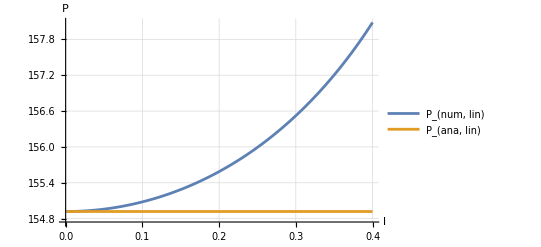

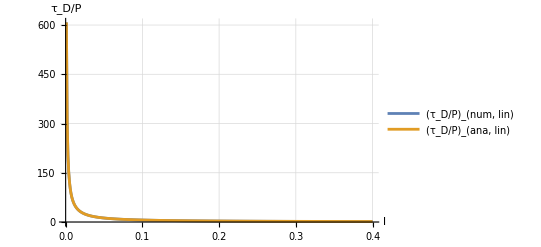

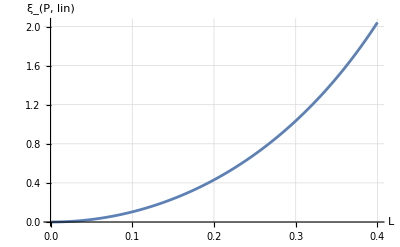

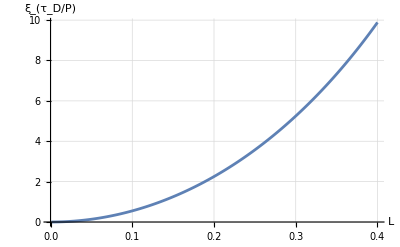

```mathematica
ListLinePlot[{PLinNumlist,PLinAnalist},AxesLabel->{"l","P"},PlotLegends->{"P_(num, lin)","P_(ana, lin)"},PlotRange->All,GridLines->Automatic]
ListLinePlot[{DampLinNumlist,DampLinAnalist},AxesLabel->{"l","τ_D/P"},PlotLegends->{"(τ_D/P)_(num, lin)","(τ_D/P)_(ana, lin)"},PlotRange->All,GridLines->Automatic]
ListLinePlot[ErrorPLinlist,AxesLabel->{"L","ξ_(P, lin)"},PlotRange->All,GridLines->Automatic]
ListLinePlot[ErrorDampLinlist,AxesLabel->{"L","ξ_(τ_D/P)"},PlotRange->All,GridLines->Automatic]
```

As for the results between density variations profiles, they only change in magnitude, maintaining the same behavior.

Regarding the accuracy of the approximations between density variations profiles,  they maintain the same behavior but the magnitude of the errors are bigger in this case, proving that the approximations are of slightly worse quality in this density profile. This coincides with the concepts of the pdf files.